# Open XXZ chain: sectors, eigenstate entropies, and edge evolution

Evaluate definitions 1–2 once. The sweep (3–4) and evolution (5–7) have independent parameters and diagonalizations. Execution is split into editable cells.

## 1. Physics definitions

### Hamiltonian and numerical utilities

Open chain, total size L. S=σ/2, ℏ=1. H=J Σⱼ(SˣⱼSˣⱼ₊₁+SʸⱼSʸⱼ₊₁+ΔSᶻⱼSᶻⱼ₊₁)+h ΣⱼSᶻⱼ+bLeft Sᶻ₁+bRight SᶻL. The system is {1,L}; the environment is {2,…,L−1}. J is signed.

```mathematica
ClearAll[check,realQ,id,maxAbs,herm,ketRho,siteOp,bondOp,xxzH,
 partitionFactor,reducedState,reducedKet,edgeRho,entropy,halfEntropy,edgeEntropy,
 traceA,traceB,ptB,negativity,concurrence,productKet,neel,helix,stateFactor,joinStates,
 charges,splitCharge,fixSign,diagonalizeBlock,sectorED,eigenket,groundKet,
 addEntropies,sweepLabels,packSweep,sweepPoint,sameSpectrum,sectorTable,
 makeEngine,evolve,evolveBatch,observables,timeChunk,timeGrid,startKernels,
 sweepParallel,evolveChunks,u1Check,realSectorCheck];
```

```mathematica
(* Stop the current cell if an input or validation fails. *)
check[test_,message_] := If[!TrueQ[test],Print[Style[message,Red ]];Abort[]];
realQ[x_] := NumericQ[x] && NumberQ[N[x ]] && TrueQ[Im[N[x ]]==0];
id[n_] := SparseArray[Band[{1,1}]->1,{n,n}];
maxAbs[a_] := If[Head[a]===SparseArray,
 Max[0,Sequence@@Abs[a["NonzeroValues"]]],Max[0,Sequence@@Abs[Flatten[a ]]]];
herm[a_] := (a+ConjugateTranspose[a])/2;
ketRho[v_] := Outer[Times,v,Conjugate[v ]];
```

```mathematica
(* Embed a one-spin or nearest-neighbour operator. *)
siteOp[a_,k_,l_] := KroneckerProduct[id[2^(k-1)],SparseArray[a],id[2^(l-k)]];
bondOp[a_,b_,k_,l_] := KroneckerProduct[
 id[2^(k-1)],SparseArray[a],SparseArray[b],id[2^(l-k-1)]];
```

```mathematica
(* Full open-chain XXZ Hamiltonian. *)
xxzH[p_Association] := Module[{l=p["L"],d=p["Delta"],h,x,y,z},
 check[IntegerQ[l] && l>=3,"L must be an integer >=3."];
 check[AllTrue[Lookup[p,{"J","Delta","h","bLeft","bRight"}],realQ],
  "J, Delta and fields must be finite real numbers."];
 {x,y,z}=Table[PauliMatrix[k]/2,{k,3}]; h=SparseArray[{}, {2^l,2^l}];
 Do[h+=p["J"](bondOp[x,x,k,l]+bondOp[y,y,k,l]+d bondOp[z,z,k,l]),{k,l-1}];
 Do[h+=p["h"] siteOp[z,k,l],{k,l}];
 SparseArray[h+p["bLeft"] siteOp[z,1,l]+p["bRight"] siteOp[z,l,l ]]
];
```

```mathematica
(* Reject Hamiltonians that the real, magnetization-block solver cannot represent. *)
u1Check[h_,l_Integer,tol_] := Module[{a=SparseArray[h],nd,off,scale,leak},
 check[Dimensions[a]=={2^l,2^l},"Hamiltonian dimensions do not match L."];
 nd=Total /@ IntegerDigits[Range[0,2^l-1],2,l];
 off=Select[Most[ArrayRules[a]],nd[[#[[1,1]]]]!=nd[[#[[1,2]]]]&];
 scale=Max[1.,Norm[a,Infinity]];leak=If[off==={},0.,Max[Abs[Last /@ off]]];
 check[leak<=tol scale,
  "H mixes total-Sz sectors. This solver would drop matrix elements. Use a solver for the surviving symmetries or full ED."];
 <|"MaxOffBlockElement"->leak,"Scale"->scale,"RelativeLeakage"->leak/scale,"Passed"->True|>
];
realSectorCheck[h_,l_Integer,tol_] := Module[{a=SparseArray[h],u,scale},
 u=u1Check[a,l,tol];scale=Max[1.,Norm[a,Infinity]];
 check[maxAbs[a-ConjugateTranspose[a]]<=tol scale,"H must be Hermitian before block diagonalization."];
 check[maxAbs[Im[a]]<=tol scale,
  "The legacy fixSign solver requires a real Hamiltonian. Complex Hermitian models need phase-preserving eigenvectors."];
 u
];
```

### Reduced density matrix

```mathematica
(* Coefficient matrix for a chosen set of sites; rho=A.A†. *)
partitionFactor[fac_,sites_List,l_Integer] := Module[{r=Dimensions[fac][[2]],rest},
 rest=Complement[Range[l],sites];
 ArrayReshape[Transpose[ArrayReshape[fac,Join[ConstantArray[2,l],{r}]],
  Ordering[Join[sites,rest,{l+1}]]],{2^Length[sites],2^Length[rest] r}]
];
reducedState[fac_,sites_List,l_Integer] := With[{a=partitionFactor[fac,sites,l]},
 a . ConjugateTranspose[a ]];
reducedKet[v_,sites_List,l_Integer] := reducedState[Transpose[{v}],sites,l];
edgeRho[v_,l_Integer] := reducedKet[v,{1,l},l];
```

```mathematica
(* Single-edge reductions, in edge basis {00,01,10,11}. *)
traceB[r_] := {{r[[1,1]]+r[[2,2]],r[[1,3]]+r[[2,4]]},
 {r[[3,1]]+r[[4,2]],r[[3,3]]+r[[4,4]]}};
traceA[r_] := {{r[[1,1]]+r[[3,3]],r[[1,2]]+r[[3,4]]},
 {r[[2,1]]+r[[4,3]],r[[2,2]]+r[[4,4]]}};
```

### Entanglement computations

```mathematica
(* Von Neumann entropy, natural logarithms. *)
entropy[r_] := Module[{e=Select[Re[Eigenvalues[N[herm[r ]]]],#>0&]},
 If[e==={},0.,-Total[e Log[e ]]]];

(* Pure-state entropy for sites 1,...,floor(L/2). *)
halfEntropy[v_,l_] := Module[{p},
 p=Select[SingularValueList[ArrayReshape[v,{2^Floor[l/2],2^Ceiling[l/2]}]]^2,#>0&];
 If[p==={},0.,-Total[p Log[p ]]]];

(* Pure-state entanglement of both edges together versus the middle. *)
edgeEntropy[v_,l_] := entropy[edgeRho[v,l ]];
```

```mathematica
(* Negativity between spin 1 and spin L. *)
ptB[r_] := ArrayReshape[Transpose[ArrayReshape[r,{2,2,2,2}],{1,4,3,2}],{4,4}];
negativity[r_] := Total[Clip[-Re[Eigenvalues[herm[ptB[r ]]]],{0,Infinity}]];

(* Concurrence from an exact reduced-state factor; stable at rank deficiency. *)
concurrence[a_] := Module[{q,r,f,s},
 {q,r}=QRDecomposition[ConjugateTranspose[a ]]; f=ConjugateTranspose[r];
 s=PadRight[Reverse[Sort[SingularValueList[
  Transpose[f] . KroneckerProduct[PauliMatrix[2],PauliMatrix[2]] . f,Tolerance->0]]],4];
 Max[0.,First[s]-Total[Rest[s ]]]
];
```

### Initial states construction

```mathematica
(* Tensor product of normalized local spinors. *)
productKet[locals_List] := Module[{v},
 check[Length[locals]>0 && AllTrue[locals,
  VectorQ[#,NumericQ] && Length[#]==2 && Norm[#]>0&],"Invalid local spinor."];
 v=Fold[Flatten[KroneckerProduct[#1,N[#2/Norm[#2 ]]]]&,{1.},locals]; v/Norm[v]
];

(* first=0 starts with up; first=1 starts with down. *)
neel[n_Integer,first_:0] := productKet[Table[UnitVector[2,1+Mod[k-1+first,2]],{k,n}]];
(* phi is the azimuth of the first spin in this vector. *)
helix[n_Integer,q_,theta_:Pi/2,phi_:0] := productKet[
 Table[{Cos[theta/2],Exp[I(phi+(k-1)q)] Sin[theta/2]},{k,n}]];
```

```mathematica
(* Accept a vector or a positive, trace-one density matrix. *)
stateFactor[input_,dim_,tol_] := Module[{x=N[Normal[input ]],e,v,keep},
 If[VectorQ[x,NumericQ],check[Length[x]==dim && Norm[x]>0,"Invalid state vector."];
  Return[Transpose[{x/Norm[x]}]]];
 check[MatrixQ[x,NumericQ] && Dimensions[x]=={dim,dim},"Invalid density-matrix dimensions."];
 check[Norm[x-ConjugateTranspose[x],"Frobenius"]<=tol && Abs[Tr[x]-1]<=tol,
  "Density matrix must be Hermitian with trace one."];
 {e,v}=Eigensystem[herm[x ]];check[Min[Re[e ]]>=-tol,"Density matrix is not positive."];
 e=Clip[Re[e],{0,Infinity}];e/=Total[e];keep=Select[Range[dim],e[[# ]]>0&];
 Transpose[Sqrt[e[[keep ]]] v[[keep ]]]
];
(* Reorder (edge 1,edge L,middle) to physical sites 1,...,L. *)
joinStates[ef_,mf_,l_] := Module[{a=KroneckerProduct[ef,mf]},
 ArrayReshape[Transpose[ArrayReshape[a,{2,2,2^(l-2),Dimensions[a][[2]]}],
  {1,3,2,4}],{2^l,Dimensions[a][[2]]}]
];
```

### Basis adaptation respecting symmetries

```mathematica
(* Charges allowed by the effective longitudinal fields. *)
charges[p_] := Module[{l=p["L"],d=2^p["L"],r,f,fields,out=<||>,st,sx,sy,sz},
 fields=ConstantArray[p["h"],l];fields[[1]]+=p["bLeft"];fields[[-1]]+=p["bRight"];
 r=SparseArray[Table[{1+FromDigits[Reverse[IntegerDigits[k,2,l ]],2],k+1}->1,
  {k,0,d-1}],{d,d}];
 f=SparseArray[Table[{d-k,k+1}->1,{k,0,d-1}],{d,d}];
 If[And@@MapThread[TrueQ[#1==#2]&,{fields,Reverse[fields]}],AssociateTo[out,"R"->r ]];
 If[And@@(TrueQ[#==0]& /@ fields),AssociateTo[out,"F"->f ]];
 If[And@@MapThread[TrueQ[#1 == -#2]&,{fields,Reverse[fields]}] &&
  !(KeyExistsQ[out,"R"] && KeyExistsQ[out,"F"]),AssociateTo[out,"RF"->r . f]];
 If[(TrueQ[p["Delta"]==1] || TrueQ[p["Delta"] == -1]) && And@@(TrueQ[#==First[fields ]]& /@ fields),
  st=If[TrueQ[p["Delta"]==1],ConstantArray[1,l],Table[(-1)^(k-1),{k,l}]];
  sx=Total[Table[st[[k ]] siteOp[PauliMatrix[1]/2,k,l],{k,l}]];
  sy=Total[Table[st[[k ]] siteOp[PauliMatrix[2]/2,k,l],{k,l}]];
  sz=Total[Table[siteOp[PauliMatrix[3]/2,k,l],{k,l}]];
  AssociateTo[out,If[TrueQ[p["Delta"]==1],"S2","StaggeredS2"]->(sx . sx+sy . sy+sz . sz)]];
 out
];
```

```mathematica
(* Split a charge eigenspace; no energy eigenvectors are mixed here. *)
splitCharge[s_,q_,name_,tol_] := Module[{b=s["Basis"],e,v,order,groups,label},
 {e,v}=Eigensystem[N[herm[ConjugateTranspose[b] . q . b]]];
 order=Ordering[Re[e ]];e=Re[e[[order ]]];v=v[[order ]];
 groups=Split[Range[Length[e ]],Abs[e[[#1 ]]-e[[#2 ]]]<tol&];
 Table[label=If[MemberQ[{"S2","StaggeredS2"},name],
   Round[(-1+Sqrt[1+4 Mean[e[[g ]]]])/2,1/2],Round[Mean[e[[g ]]]]];
  <|"Basis"->b . Transpose[Orthogonalize[v[[g ]]]],"Labels"->Append[s["Labels"],
   Switch[name,"S2","S","StaggeredS2","StaggeredS",_,name]->label]|>,{g,groups}]
];
(* The Hamiltonian is real symmetric; retain real packed vectors. *)
fixSign[v_] := Module[{w=Re[N[v ]],k},
 k=First[Ordering[Abs[w],-1]];Developer`ToPackedArray[If[w[[k ]]<0,-w,w ]]
];
```

### Diagonalizations

```mathematica
(* Raw eigenpairs in one resolved sector; preserve arbitrarily small gaps. *)
diagonalizeBlock[s_,hm_,ids_,tol_] := Module[{b=s["Basis"],h,e,v,order,rows,gaps,res,orth,leak,scale},
 h=herm[ConjugateTranspose[b] . hm . b];{e,v}=Eigensystem[N[h ]];
 order=Ordering[Re[e ]];e=Developer`ToPackedArray[Re[e[[order ]]]];
 rows=fixSign /@ Transpose[b . Transpose[v[[order ]]]];
 rows=Developer`ToPackedArray[rows];scale=Max[1.,Norm[hm,Infinity ]];
 res=Max[MapThread[Norm[hm . #2-#1 #2]&,{e,rows}]];
 orth=maxAbs[rows . ConjugateTranspose[rows]-IdentityMatrix[Length[rows ]]];
 leak=maxAbs[hm . b-b . h];
 check[res<100 tol scale && orth<100 tol && leak<100 tol scale,"Sector validation failed."];
 gaps=Select[Differences[e],#>0&];
 <|"Labels"->s["Labels"],"Dimension"->Length[e],"Indices"->ids,
  "Eigenvalues"->e,"Vectors"->rows,"Residual"->res,"OrthogonalityError"->orth,
  "MinPositiveGap"->If[gaps==={},Missing["NoGap"],Min[gaps ]]|>
];
```

```mathematica
(* Full independent ED of every surviving symmetry sector. *)
sectorED[p_Association,tol_:10^-10] := Module[
 {l=p["L"],h,q,active,out={},ids,hm,m,names,spaces},
 h=xxzH[p];realSectorCheck[h,l,tol];q=charges[p];
 active=Select[Keys[q],maxAbs[h . q[#]-q[#] . h]<tol Max[1.,Norm[h,Infinity ]]&];
 Do[m=l/2-nDown;ids=Select[Range[2^l],Total[IntegerDigits[#-1,2,l ]]==nDown&];
  hm=N[Normal[h[[ids,ids ]]]];
  names=Select[active,!MemberQ[{"F","RF"},#] || m==0&];
  names=SortBy[names,Switch[#,"S2"|"StaggeredS2",0,"R",1,_,2]&];
  spaces={<|"Basis"->IdentityMatrix[Length[ids ]],"Labels"-><|"m"->m|>|>};
  Do[spaces=Flatten[splitCharge[#,N[Normal[q[name][[ids,ids ]]]],name,tol]& /@ spaces,1],
   {name,names}];
  out=Join[out,diagonalizeBlock[#,hm,ids,tol]& /@ spaces],{nDown,0,l}];
 check[Total[Lookup[out,"Dimension"]]==2^l,"Incomplete sector dimensions."];
 <|"Parameters"->p,"Hamiltonian"->h,"ActiveCharges"->active,"Sectors"->out,
  "DimensionSum"->Total[Lookup[out,"Dimension"]]|>
];
(* Full vector from the chosen sector and its energy-order index. *)
eigenket[ed_,sector_Integer,level_Integer] := With[{s=ed["Sectors"][[sector ]]},
 Normal[SparseArray[Thread[s["Indices"]->s["Vectors"][[level ]]],{2^ed["Parameters"]["L"]}]]];
sectorTable[ed_] := MapIndexed[<|"Sector"->First[#2],"Labels"->#1["Labels"],
 "Dimension"->#1["Dimension"],"Emin"->First[#1["Eigenvalues"]],
 "Emax"->Last[#1["Eigenvalues"]],"MinPositiveGap"->#1["MinPositiveGap"],
 "Residual"->#1["Residual"]|>&,ed["Sectors"]];
```

### Diagonalization special cases and eigenstate entropies

At Δ=1, uniform effective fields permit S labels; at Δ=−1 they permit staggered S labels. At m=0, F or RF may also be used. Exact degenerate eigenstate entropies depend on the chosen raw eigensystem basis. No near-degenerate energy vectors are canonicalized.

```mathematica
(* One ground-state vector; ties follow sector order, then energy order. *)
groundKet[ed_] := Module[{pairs,c},
 pairs=Flatten[Table[{ed["Sectors"][[k ]]["Eigenvalues"][[r ]],k,r},
  {k,Length[ed["Sectors"]]},{r,ed["Sectors"][[k ]]["Dimension"]}],1];
 c=First[SortBy[pairs,First ]];eigenket[ed,c[[2]],c[[3]]]
];
(* Add both pure-eigenstate entropies to an ED result. *)
addEntropies[ed_] := Module[{out=ed,l=ed["Parameters"]["L"],s,v},
 out["Sectors"]=Table[s=ed["Sectors"][[k ]];
  v=Table[eigenket[ed,k,r],{r,s["Dimension"]}];
  Join[s,<|"HalfEntropy"->(halfEntropy[#,l]& /@ v),
   "EdgesEntropy"->(edgeEntropy[#,l]& /@ v)|>],{k,Length[ed["Sectors"]]}];out
];
```

```mathematica
(* Parent labels remain valid along the Delta sweep. *)
sweepLabels[a_] := KeySort[KeyDrop[a,{"S","StaggeredS"}]];
packSweep[ed_] := Module[{groups},
 groups=GatherBy[ed["Sectors"],ToString[Normal[sweepLabels[#["Labels"]]],InputForm]&];
 Association[Table[With[{a=SortBy[Flatten[
  Table[Transpose[{s["Eigenvalues"],s["HalfEntropy"],s["EdgesEntropy"]}],{s,g}],1],First]},
  ToString[Normal[sweepLabels[First[g]["Labels"]]],InputForm]->
   <|"Labels"->sweepLabels[First[g]["Labels"]],"Energies"->a[[All,1]],
    "HalfEntropy"->a[[All,2]],"EdgesEntropy"->a[[All,3]]|>],{g,groups}]]
];
sweepPoint[d_,p_,tol_] := packSweep[addEntropies[sectorED[Join[p,<|"Delta"->d|>],tol ]]];
(* Compare complete sorted spectra on the sampled grid. *)
sameSpectrum[a_,b_,samples_,tol_] := Module[{ea,eb},
 ea=(#[a]["Energies"]& /@ samples);eb=(#[b]["Energies"]& /@ samples);
 Dimensions[ea]===Dimensions[eb] && maxAbs[ea-eb]<tol Max[1.,maxAbs[{ea,eb}]]
];
```

### Evolution procedure

```mathematica
(* Keep sector vectors and coefficients; skip only exactly zero projections. *)
makeEngine[ed_,fac_] := Module[{blocks={},c},
 realSectorCheck[ed["Hamiltonian"],ed["Parameters"]["L"],10^-10];
 Do[c=Conjugate[s["Vectors"]] . fac[[s["Indices"],All ]];
  If[maxAbs[c]>0,AppendTo[blocks,<|"Indices"->s["Indices"],"E"->s["Eigenvalues"],
   "V"->Developer`ToPackedArray[Transpose[s["Vectors"]]],
   "C"->Developer`ToPackedArray[c]|>]],{s,ed["Sectors"]}];
 <|"Parameters"->ed["Parameters"],"L"->ed["Parameters"]["L"],"Dimension"->Length[fac],
  "Columns"->Dimensions[fac][[2]],"Sectors"->blocks|>
];
(* Single-time evolution, useful for checks and direct access. *)
evolve[t_,engine_] := Module[{a},
 a=ConstantArray[0.+0.I,{engine["Dimension"],engine["Columns"]}];
 Do[a[[s["Indices"],All ]]+=s["V"] . (Exp[-I s["E"] t] s["C"]),{s,engine["Sectors"]}];a
];
(* Batch matrix products over time; a[[All,All,k]] is the kth factor. *)
evolveBatch[times_List,engine_] := Module[{a,ph},
 a=ConstantArray[0.+0.I,{engine["Dimension"],engine["Columns"],Length[times]}];
 Do[ph=Exp[-I Outer[Times,s["E"],N[times ]]];
  Do[a[[s["Indices"],c,All ]]+=s["V"] . (ph s["C"][[All,c ]]),{c,engine["Columns"]}],
  {s,engine["Sectors"]}];a
];
```

```mathematica
(* Edge observables from the 4 x environment-rank coefficient matrix. *)
observables[t_,a_,rho0_] := Module[{r,a1,b1,sa,sb,sab,z,x,ma,mb,e},
 r=a . ConjugateTranspose[a];a1=traceB[r];b1=traceA[r];
 {sa,sb,sab}=entropy /@ {a1,b1,r};{x,z}=PauliMatrix /@ {1,3};
 ma=Re[Tr[z . a1]];mb=Re[Tr[z . b1]];e=Reverse[Sort[Re[Eigenvalues[herm[r ]]]]];
 <|"Time"->t,"RhoAB"->r,"RhoA"->a1,"RhoB"->b1,"EigenvaluesAB"->e,
  "Purity"->Re[Tr[r . r]],"EntropyA"->sa,"EntropyB"->sb,"EntropyAB"->sab,
  "MutualInfo"->sa+sb-sab,"Concurrence"->concurrence[a],"Negativity"->negativity[r],
  "InitialOverlap"->Re[Tr[rho0 . r]],"MagnetizationA"->ma,"MagnetizationB"->mb,
  "ConnectedZZ"->Re[Tr[KroneckerProduct[z,z] . r]]-ma mb,
  "ConnectedXX"->Re[Tr[KroneckerProduct[x,x] . r]]-Re[Tr[x . a1]] Re[Tr[x . b1]],
  "TraceError"->Abs[Tr[r]-1.],"HermiticityError"->Norm[r-ConjugateTranspose[r],"Frobenius"],
  "MinEigenvalue"->Last[e]|>
];
timeChunk[times_,engine_,rho0_,tol_] := Module[{a,records},
 a=evolveBatch[times,engine];
 records=Table[observables[times[[k ]],partitionFactor[a[[All,All,k ]],
  {1,engine["L"]},engine["L"]],rho0],{k,Length[times]}];
 check[Max[Lookup[records,"TraceError"]]<tol &&
  Max[Lookup[records,"HermiticityError"]]<tol && Min[Lookup[records,"MinEigenvalue"]]>=-tol,
  "Reduced-state validation failed."];records
];
```

```mathematica
(* Linear or logarithmic sampling, including t=0. Linear dt is nominal: the last step may be shorter. *)
timeGrid[cfg_] := Module[{t},
 check[realQ[cfg["tMax"]] && cfg["tMax"]>0,"tMax must be positive."];
 Switch[cfg["Grid"],"Linear",
  check[realQ[cfg["dt"]] && cfg["dt"]>0,"dt must be positive."];
  t=N[cfg["dt"] Range[0,Floor[cfg["tMax"]/cfg["dt"]]]];
  If[Abs[Last[t]-cfg["tMax"]]<10^-12 Max[1.,cfg["tMax"]],
   t[[-1]]=N[cfg["tMax"]],AppendTo[t,N[cfg["tMax"]]]];t,
 "Log",check[0<cfg["tMinPositive"]<cfg["tMax"] && IntegerQ[cfg["LogPoints"]] &&
   cfg["LogPoints"]>=2,"Invalid logarithmic grid."];
  t=Join[{0.},Exp[Subdivide[Log[N[cfg["tMinPositive"]]],Log[N[cfg["tMax"]]],cfg["LogPoints"]-1]]];
  t[[-1]]=N[cfg["tMax"]];t,
 _,check[False,"Grid must be Linear or Log."]]
];
```

### Time splitting and parallelization

```mathematica
(* Reuse existing kernels; no kernels are closed. *)
startKernels[cfg_] := Module[{n},
 If[!TrueQ[cfg["Enabled"]],Return[0]];
 n=Length[Kernels[]];If[n<cfg["Kernels"],Quiet[LaunchKernels[cfg["Kernels"]-n ]]];
 n=Length[Kernels[]];Print["Available parallel kernels: ",n];n
];
(* Independent Delta points; full eigenvectors are computed at each point. *)
sweepParallel[grid_,p_,tol_,cfg_] := Module[{n},
 n=startKernels[cfg];
 If[n<2,Return[sweepPoint[#,p,tol]& /@ grid]];
 DistributeDefinitions[sweepPoint];
 With[{pp=p,tt=tol},ParallelMap[sweepPoint[#,pp,tt]&,grid,Method->"CoarsestGrained"]]
];
```

```mathematica
(* Batches limit memory; each worker gets one engine copy. *)
evolveChunks[times_,engine_,rho0_,tol_,cfg_] := Module[
 {n,batch,room,chunks,packets,records,reference,error},
 n=startKernels[cfg];room=cfg["MemoryBudgetGB"] 1024.^3;
 If[n>=2 && 4. n ByteCount[engine]>room,
  Print["Engine copies exceed the memory budget; using serial batches."];n=0];
 batch=Min[cfg["BatchTimes"],Max[1,Floor[room/
  (4. Max[1,n] 16 engine["Dimension"] engine["Columns"])]]];
 chunks=Partition[times,UpTo[batch ]];
 Print["Time batches: ",Length[chunks],"; maximum points per batch: ",batch];
 If[n>=2,
  (* Clear both worker values and their recorded definitions before reuse. *)
  Clear[sharedEngine,sharedRho0,sharedTolerance];
  DistributeDefinitions[sharedEngine,sharedRho0,sharedTolerance];
  sharedEngine=engine;sharedRho0=rho0;sharedTolerance=tol;
  DistributeDefinitions[timeChunk,sharedEngine,sharedRho0,sharedTolerance];
  packets=ParallelMap[timeChunk[#,sharedEngine,sharedRho0,sharedTolerance]&,
   chunks,Method->"CoarsestGrained"];
  Clear[sharedEngine,sharedRho0,sharedTolerance];
  DistributeDefinitions[sharedEngine,sharedRho0,sharedTolerance],
  packets=timeChunk[#,engine,rho0,tol]& /@ chunks];
 check[AllTrue[packets,ListQ],"A time batch failed."];
 records=Flatten[packets,1];check[Lookup[records,"Time"]===times,"Time ordering failed."];
 reference=Table[observables[t,partitionFactor[evolve[t,engine],{1,engine["L"]},engine["L"]],rho0],
  {t,{First[times],Last[times]}}];
 error=Max[MapThread[Norm[#1["RhoAB"]-#2["RhoAB"],"Frobenius"]&,
  {{First[records],Last[records]},reference}]];
 check[error<tol,"Batched/single-time endpoint comparison failed."];records
];
```

## 2. Plotting, MaTeX labels, and file output

### Labels and ticks

```mathematica
ClearAll[tex,texNumber,ticks,logTicks,sectorLabel,dimLabel,caption,curveStyles,pointMarkers,
 framePlot,plotPanel,sweepPanels,fixedPanels,series,matrixSeries,densityPanels,
 safeToken,newFolder,baseFolder,savePNG];
texReady=Automatic;
(* MaTeX labels; a visible native fallback is used if MaTeX is unavailable. *)
tex[s_String,size_:16] := Module[{g},
 If[texReady===Automatic,
  texReady=Quiet[Check[Needs["MaTeX`"];True,False ]];
  If[!TrueQ[texReady],Print["MaTeX unavailable: check the local installation."]]];
 If[TrueQ[texReady],g=Quiet[Check[MaTeX`MaTeX[s,FontSize->size],$Failed ]];
  If[MatchQ[g,_Graphics],Return[g ]];
  texReady=False;Print["MaTeX failed: check TeX/Ghostscript."]];
 Style[s,Black,FontFamily->"Times",FontSize->size]
];
```

```mathematica
(* Numeric labels use decimals rather than fractions. *)
texNumber[x_] := Module[{s,p},
 If[TrueQ[x==0],Return["0"]];
 If[TrueQ[x==Round[x ]] && Abs[x]<10^6,Return[ToString[Round[x ]]]];
 s=StringReplace[ToString[N[x],InputForm],RegularExpression["`[0-9.]*"]->""];
 p=StringSplit[s,"*^"];p[[1]]=StringReplace[p[[1]],RegularExpression["\\.$"]->""];
 If[Length[p]==2,p[[1]]<>"\\times 10^{"<>p[[2]]<>"}",First[p ]]
];
ticks[lo_?NumericQ,hi_?NumericQ] := Module[{a=lo,b=hi},
 If[a==b,a-=1;b+=1];
 ({#,tex[texNumber[#],14],{.012,0}}& /@ FindDivisions[{a,b},5])];
logTicks[lo_?NumericQ,hi_?NumericQ] :=
 ({N[# Log[10]],tex["10^{"<>ToString[#]<>"}",14],{.012,0}}& /@
  Range[Floor[lo/Log[10]],Ceiling[hi/Log[10]]]);
sectorLabel[a_] := StringRiffle[KeyValueMap[
 Switch[#1,"R","r","F","f","RF","rf","StaggeredS","S_{\\rm stag}",_,#1]<>
  "="<>texNumber[#2]&,a],",\\quad "];
(* A common dimension for equivalent sectors; otherwise use legend order. *)
dimLabel[dims_List] := If[SameQ@@dims,
 "d_{\\mathrm{sector}}="<>ToString[First[dims]],
 StringRiffle[MapIndexed["d_{"<>ToString[First[#2]]<>"}="<>ToString[#1]&,dims],",\\quad "]];
```

```mathematica
(* Every caption uses the parameters of the computed result. *)
caption[p_,deltaText_,extra_:""] := Column[
 tex[#,13]& /@ DeleteCases[{
 "\\mathrm{XXZ~OBC}:\\quad L="<>texNumber[p["L"]]<> ",\\quad J="<>texNumber[p["J"]]<>
  ",\\quad J_z=J\\Delta,\\quad S^a=\\sigma^a/2",
 "h="<>texNumber[p["h"]]<> ",\\quad b_L="<>texNumber[p["bLeft"]]<>
  ",\\quad b_R="<>texNumber[p["bRight"]]<> ",\\quad AB=\\{1,L\\}",
 deltaText,extra},""],Alignment->Center,Spacings->.3];
curveStyles[n_] := Table[Switch[k,
 1,Directive[Blue,AbsoluteThickness[2]],
 2,Directive[Orange,AbsoluteThickness[2],Dashed],
 _,Directive[ColorData[97][k],AbsoluteThickness[2],Dashing[{.012,.004,.003,.004}]]],{k,n}];
(* Filled and larger open markers keep overlapping sectors visible. *)
pointMarkers[n_] := Table[{Switch[k,1,"●",2,"□",_,"◇"],
 Switch[k,1,12,2,18,_,22]},{k,n}];
```

### Framed plots and export layout

```mathematica
(* Build tick lists before export; logarithmic plots use log(t) coordinates. *)
framePlot[data_,xlabel_,ylabel_,styles_,legends_,joined_:True,log_:False,markers_:Automatic,topLabel_:""] :=
 Module[{curves=Map[{#[[1]],Chop[#[[2]],plotChop]}&,data,{2}],points,xr,yr,xt,yt},
  If[log,curves=Map[{Log[#[[1]]],#[[2]]}&,curves,{2}]];
  points=Flatten[curves,1];xr=MinMax[points[[All,1]]];yr=MinMax[points[[All,2]]];
  xt=If[log,logTicks@@xr,ticks@@xr];yt=ticks@@yr;
  ListLinePlot[curves,Joined->joined,InterpolationOrder->1,
   PlotStyle->styles,PlotMarkers->If[joined,None,markers],
   Frame->True,Axes->False,PlotRange->All,RotateLabel->True,
   FrameLabel->{{tex[ylabel,19],None},{tex[xlabel,20],None}},
   FrameTicks->{{yt,None},{xt,None}},
   PlotLabel->If[topLabel=="",None,tex[topLabel,15]],
   FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
   ImagePadding->{{140,40},{100,50}},PlotRangePadding->Scaled[.04],
   PlotLegends->If[legends==={},None,
    Placed[If[joined,LineLegend[styles,tex[#,15]& /@ legends,LegendLayout->"Column"],
     PointLegend[styles,tex[#,15]& /@ legends,
      LegendMarkers->If[ListQ[markers],First /@ markers,Automatic],LegendMarkerSize->12,
      LegendLayout->"Column"]],Right ]],
   ImageSize->1100,AspectRatio->.52,Background->White]
 ];
plotPanel[title_,cap_,g_] := Column[{tex[title,22],cap,g},
 Alignment->Center,Spacings->.6];
savePNG[file_,panel_] := check[StringQ[Quiet[Check[
 Export[file,panel,"PNG",ImageResolution->150],$Failed ]]],"PNG export failed: "<>file];
```

### Spectrum and eigenstate-entropy plots

```mathematica
(* One panel per group; members keep distinct styles. *)
sweepPanels[data_,grid_,groups_,p_,key_,ylabel_,title_] := Module[
 {styles,labels,curves,lineStyles,values,branches,markers,groupMarkers,dimText},
 Table[styles=curveStyles[Length[group ]];groupMarkers=pointMarkers[Length[group ]];
  labels=sectorLabel[First[data][#]["Labels"]]& /@ group;
  dimText=dimLabel[Length[First[data][#]["Energies"]]& /@ group];
  curves={};lineStyles={};markers={};
  Do[values=(#[group[[k ]]][key]& /@ data);
   branches=(Transpose[{N[grid],#}]& /@ Transpose[values]);
   curves=Join[curves,branches];
   lineStyles=Join[lineStyles,ConstantArray[styles[[k ]],Length[branches ]]];
   markers=Join[markers,ConstantArray[groupMarkers[[k ]],Length[branches ]]],{k,Length[group]}];
  plotPanel[title,caption[p,"\\Delta\\in["<>texNumber[First[grid ]]<>","<>
   texNumber[Last[grid ]]<>"];\\quad N_\\Delta="<>ToString[Length[grid ]]],
   Legended[framePlot[curves,"\\Delta",ylabel,lineStyles,{},key=="Energies",False,markers,dimText],
    Placed[If[key=="Energies",LineLegend[styles,tex[#,15]& /@ labels],
     PointLegend[styles,tex[#,15]& /@ labels,
      LegendMarkers->First /@ groupMarkers,LegendMarkerSize->12]],Right ]]],{group,groups}]
];
(* Fixed-Delta entropy or energy versus energy-order index. *)
fixedPanels[ed_,groups_,key_,ylabel_,title_] := Module[{styles,labels,data,s,groupMarkers,dimText},
 Table[styles=curveStyles[Length[group ]];groupMarkers=pointMarkers[Length[group]];
  labels=sectorLabel[ed["Sectors"][[#]]["Labels"]]& /@ group;
  dimText=dimLabel[ed["Sectors"][[#]]["Dimension"]& /@ group];
  data=Table[s=ed["Sectors"][[k ]];Transpose[{Range[s["Dimension"]],s[key]}],{k,group}];
  plotPanel[title,caption[ed["Parameters"],"\\Delta="<>texNumber[ed["Parameters"]["Delta"]]],
   framePlot[data,"n\\quad(\\text{energy order})",ylabel,styles,labels,key=="Eigenvalues",False,groupMarkers,dimText ]],
  {group,groups}]
];
```

### Evolution plot definitions

```mathematica
series[records_,key_] := ({#["Time"],#[key]}& /@ records);
matrixSeries[records_,key_,i_,j_,part_] := ({#["Time"],part[#[key][[i,j ]]]}& /@ records);
(* Each entry is {filename,title,y label,data,legend labels}. *)
densityPanels[records_,p_,time_,log_:False] := Module[
 {specs={},basis={"00","01","10","11"},pairs=Subsets[Range[4],{2}],labels,partData,add,
  styles,data,g,note},
 add[name_,title_,ylabel_,curves_,legends_] := AppendTo[specs,{name,title,ylabel,curves,legends}];
 add["01_populations","\\text{Edge populations}","\\rho_{AB;ss}(t)",
  Table[matrixSeries[records,"RhoAB",k,k,Re],{k,4}],
  ("\\rho_{"<>#<>","<>#<>"}"& /@ basis)];
 Do[labels=If[part=="Abs",
   ("|\\rho_{"<>basis[[#[[1]]]]<>","<>basis[[#[[2]]]]<>"}|"& /@ pairs),
   ("\\operatorname{"<>part<>"}\\rho_{"<>basis[[#[[1]]]]<>","<>basis[[#[[2]]]]<>"}"& /@ pairs)];
  partData=(matrixSeries[records,"RhoAB",#[[1]],#[[2]],
   Switch[part,"Re",Re,"Im",Im,"Abs",Abs ]]& /@ pairs);
  add["02_coherences_"<>part,"\\text{All six edge coherences: "<>part<>"}",
   "\\rho_{AB;ij}(t)",partData,labels],{part,{"Re","Im","Abs"}}];
 add["03_entropies_mutual_information","\\text{Entropies and mutual information}",
  "S,I\\;(\\mathrm{nats})",series[records,#]& /@ {"EntropyA","EntropyB","EntropyAB","MutualInfo"},
  {"S(\\rho_A)","S(\\rho_B)","S(\\rho_{AB})","I(A:B)"}];
 add["04_edge_entanglement","\\text{Entanglement between the edge spins}","C,\\mathcal N",
  series[records,#]& /@ {"Concurrence","Negativity"},{"C(\\rho_{AB})","\\mathcal N(\\rho_{AB})"}];
 add["05_purity_initial_overlap","\\text{Purity and reduced-state overlap}","\\text{Purity / overlap}",
  series[records,#]& /@ {"Purity","InitialOverlap"},
  {"\\operatorname{Tr}\\rho_{AB}(t)^2","\\operatorname{Tr}[\\rho_{AB}(0)\\rho_{AB}(t)]"}];
 add["06_magnetizations","\\text{Local edge magnetizations}","\\langle\\sigma^z\\rangle=2\\langle S^z\\rangle",
  series[records,#]& /@ {"MagnetizationA","MagnetizationB"},
  {"\\langle\\sigma_1^z\\rangle","\\langle\\sigma_L^z\\rangle"}];
 add["07_connected_correlations","\\text{Connected edge correlations}","\\langle\\sigma_1^k\\sigma_L^k\\rangle-\\langle\\sigma_1^k\\rangle\\langle\\sigma_L^k\\rangle",
  series[records,#]& /@ {"ConnectedZZ","ConnectedXX"},{"k=z","k=x"}];
 add["08_density_validation","\\text{Reduced-state numerical checks}","\\text{Error / minimum eigenvalue}",
  series[records,#]& /@ {"TraceError","HermiticityError","MinEigenvalue"},
  {"|\\operatorname{Tr}\\rho_{AB}-1|","\\|\\rho_{AB}-\\rho_{AB}^\\dagger\\|_F","\\lambda_{\\min}"}];
 add["09_density_eigenvalues","\\text{Edge-state eigenvalues}","\\lambda_k(\\rho_{AB})",
  Table[({#["Time"],#["EigenvaluesAB"][[k ]]}& /@ records),{k,4}],Table["\\lambda_"<>ToString[k],{k,4}]];
 Do[labels=If[part=="Abs",{"|\\rho_{A;01}|","|\\rho_{B;01}|"},
  {"\\operatorname{"<>part<>"}\\rho_{A;01}","\\operatorname{"<>part<>"}\\rho_{B;01}"}];
  add["10_local_coherences_"<>part,"\\text{Single-edge coherences: "<>part<>"}","\\rho_{Q;01}(t)",
   Table[matrixSeries[records,key,1,2,Switch[part,"Re",Re,"Im",Im,"Abs",Abs ]],
    {key,{"RhoA","RhoB"}}],labels],{part,{"Re","Im","Abs"}}];
 note="t\\in[0,"<>texNumber[time["tMax"]]<>"];\\quad N_t="<>ToString[Length[records ]]<>
  If[time["Grid"]=="Linear",";\\quad \\delta t_{\\rm nominal}="<>texNumber[time["dt"]],
   ";\\quad \\text{logarithmic sampling}"];
 Association[Table[data=If[log,Select[#,First[#]>0&]& /@ spec[[4]],spec[[4]]];
  styles=Table[Directive[ColorData[97][k],AbsoluteThickness[2]],{k,Length[data]}];
  g=framePlot[data,"t\\quad(\\hbar=1)",spec[[3]],styles,spec[[5]],True,log];
  spec[[1]]<>If[log,"_logtime",""]->plotPanel[spec[[2]],
   caption[p,"\\Delta="<>texNumber[p["Delta"]],note],g],{spec,specs}]]
];
```

### Output paths

```mathematica
baseFolder[] := Module[{d},
 d=If[StringQ[$InputFileName] && StringLength[$InputFileName]>0,
  DirectoryName[ExpandFileName[$InputFileName ]],Quiet[Check[NotebookDirectory[],Directory[]]]];
 If[StringQ[d],d,Directory[]]];
safeToken[x_] := Module[{s},
 s=StringReplace[ToString[N[x],InputForm],RegularExpression["`[0-9.]*"]->""];
 s=StringReplace[s,RegularExpression["\\.$"]->""];
 StringReplace[s,{"*^"->"e","."->"p","-"->"m","+"->""}]];
(* Numbered reruns prevent overwriting; no timestamps or random strings. *)
newFolder[root_,tag_] := Module[{d,k=1},
 d=FileNameJoin[{root,tag}];
 While[DirectoryQ[d],k++;d=FileNameJoin[{root,tag<>"_run"<>ToString[k]}]];
 CreateDirectory[d,CreateIntermediateDirectories->True];d
];
```

## 3. Common numerical and plot settings

```mathematica
edTolerance = 10^-10;
validationTolerance = 10^-8;
matchingTolerance = 10^-8;
parallel = <|"Enabled"->True,"Kernels"->12,"MemoryBudgetGB"->15.,"BatchTimes"->128|>;
plotChop = 10^-10;
exportLogTime = False;
outputRoot = FileNameJoin[{baseFolder[],"xxz_open_edges_results"}];
```

## 4. Delta sweep: independent inputs and execution

### 4.1 Choose sweep parameters

These parameters apply only to the sweep. Evolution parameters are entered separately in section 5.

```mathematica
sweepModel = <|"L"->8,"J"->1,"h"->0,"bLeft"->0,"bRight"->0|>;
deltaGrid = Range[-5,5,0.05];
(*sweepLabel = "sweep01_fieldLeft_0.1";*)
sweepLabel = "sweep01";
```

### 4.2 Diagonalize and calculate eigenstate entropies

```mathematica
sweepUsed = sweepModel;
deltaUsed = deltaGrid;
check[Length[deltaUsed]>=2 && AllTrue[deltaUsed,realQ] &&
 And@@Thread[Differences[N[deltaUsed ]]>0],"Delta grid must be strictly increasing."];
{sweepSeconds,sweepData} = AbsoluteTiming[
 sweepParallel[deltaUsed,sweepUsed,edTolerance,parallel ]];
Print["Sweep seconds: ",sweepSeconds];
```

### 4.3 Identify matching sectors

```mathematica
sweepKeys = Keys[First[sweepData ]];
check[AllTrue[sweepData,AssociationQ[#] && Sort[Keys[# ]]==Sort[sweepKeys] &&
 Total[Length[#["Energies"]]& /@ Values[# ]]==2^sweepUsed["L"]&],"Incomplete sweep."];
sweepGroups = Gather[sweepKeys,sameSpectrum[#1,#2,sweepData,matchingTolerance]&];
Print["Sectors: ",Length[sweepKeys],"; groups: ",Length[sweepGroups ]];
```

### 4.4 Energy spectra

```mathematica
spectrumPlots = sweepPanels[sweepData,deltaUsed,sweepGroups,sweepUsed,
 "Energies","E","\\text{Sector energy spectrum}"];
(* Inspect one plot before export. *)
spectrumPlots[[1]]
```

### 4.5 Half-chain eigenstate entropy

```mathematica
halfPlots = sweepPanels[sweepData,deltaUsed,sweepGroups,sweepUsed,
 "HalfEntropy","S_{\\mathrm{half}}\\;(\\mathrm{nats})","\\text{Half-chain eigenstate entanglement}"];
halfPlots[[1]]
```

### 4.6 Edges-versus-middle eigenstate entropy

```mathematica
edgeEntropyPlots = sweepPanels[sweepData,deltaUsed,sweepGroups,sweepUsed,
 "EdgesEntropy","S_{AB|E}\\;(\\mathrm{nats})","\\text{Edges versus middle eigenstate entanglement}"];
edgeEntropyPlots[[1]]
```

### 4.7 Export sweep plots and data

```mathematica
sweepDir = newFolder[outputRoot,sweepLabel<>"_L"<>ToString[sweepUsed["L"]]<>
 "_J"<>safeToken[sweepUsed["J"]]];
Do[savePNG[FileNameJoin[{sweepDir,"spectrum_group_"<>ToString[k]<>".png"}],spectrumPlots[[k ]]],
 {k,Length[spectrumPlots]}];
Do[savePNG[FileNameJoin[{sweepDir,"half_entropy_group_"<>ToString[k]<>".png"}],halfPlots[[k ]]],
 {k,Length[halfPlots]}];
Do[savePNG[FileNameJoin[{sweepDir,"edge_entropy_group_"<>ToString[k]<>".png"}],edgeEntropyPlots[[k ]]],
 {k,Length[edgeEntropyPlots]}];
Export[FileNameJoin[{sweepDir,"eigenstate_sweep.wxf"}],
 <|"Model"->sweepUsed,"DeltaGrid"->deltaUsed,"Groups"->sweepGroups,"Data"->sweepData|>,"WXF"];
Print["Saved: ",sweepDir];
```

## 5. Evolution: independent parameters and diagonalization

### 5.1 Choose the Hamiltonian for this evolution

Set all evolution parameters here, including Delta. Running the sweep is unnecessary.

```mathematica
evoModel = <|
 "L" -> 8,
 "J" -> 1,
 "Delta" -> 0.5,
 "h" -> 0,
 "bLeft" -> 0.01,
 "bRight" -> 0
|>;
evoLabel = "evolution01_fieldLeft_0.01";
```

### 5.2 Choose the evolution time grid

```mathematica
evoTime = <|
 "Grid" -> "Linear",
 "tMax" -> 400.,
 "dt" -> 0.1,
 "tMinPositive" -> 0.01,
 "LogPoints" -> 501
|>;
```

### 5.3 Diagonalize this Hamiltonian

```mathematica
evoUsed = evoModel;
{evoEDSeconds,evoED} = AbsoluteTiming[sectorED[evoUsed,edTolerance ]];
evoSectors = sectorTable[evoED];
Print["ED seconds: ",evoEDSeconds,"; tolerance: ",edTolerance];
Dataset[evoSectors]
```

### 5.4 Optional fixed-Delta eigenstate plots

```mathematica
evoEigenstates = addEntropies[evoED];
evoEnergies = Lookup[evoEigenstates["Sectors"],"Eigenvalues"];
evoGroups = Gather[Range[Length[evoEnergies ]],
 Length[evoEnergies[[#1 ]]]==Length[evoEnergies[[#2 ]]] &&
 maxAbs[evoEnergies[[#1 ]]-evoEnergies[[#2 ]]]<matchingTolerance Max[1.,maxAbs[evoEnergies ]]&];
```

```mathematica
fixedEnergyPlots = fixedPanels[evoEigenstates,evoGroups,"Eigenvalues","E_n","\\text{Sector energies}"];
fixedHalfPlots = fixedPanels[evoEigenstates,evoGroups,"HalfEntropy",
 "S_{\\mathrm{half}}\\;(\\mathrm{nats})","\\text{Half-chain eigenstate entanglement}"];
fixedEdgePlots = fixedPanels[evoEigenstates,evoGroups,"EdgesEntropy",
 "S_{AB|E}\\;(\\mathrm{nats})","\\text{Edges versus middle eigenstate entanglement}"];
```

## 6. Initial states for this evolution

### 6.1 Choose factorized or full-chain mode

```mathematica
stateMode = "Factorized";   (* Choose "Factorized" or "Full" here only. *)
```

### 6.2 State of the two edge spins

Used only in Factorized mode. Basis {00,01,10,11}; vector or 4 x 4 density matrix. One active assignment.

```mathematica
edgeState = {1,1,1,1}/2;
(* Alternatives: {0,1,1,0}/Sqrt[2], {0,0,1,0}, IdentityMatrix[4]/4. *)
```

### 6.3 State of the middle spins

Physical order {2,...,L-1}. neel[n,0] starts with up on physical site 2. A middle helix starts its phase at site 2.

```mathematica
middleState = neel[evoModel["L"]-2,0];
(* Alternatives: productKet[ConstantArray[{1,0},evoModel["L"]-2]],
   productKet[ConstantArray[{1,1},evoModel["L"]-2]], helix[evoModel["L"]-2,Pi/3]. *)
```

### 6.4 Full initial state

Used only in Full mode. This default is a non-eigenstate initial condition. To study a stationary state deliberately, replace it with groundKet[evoED] or eigenket[evoED,sector,level].

```mathematica
fullState = helix[evoModel["L"],Pi/3];
(* Alternatives: neel[evoModel["L"]], groundKet[evoED], eigenket[evoED,3,1]. *)
```

### 6.5 Assemble and inspect the initial state

```mathematica
check[evoUsed===evoModel,"Evolution parameters changed: rerun section 5.3."];
check[MemberQ[{"Factorized","Full"},stateMode],"Invalid stateMode."];
If[stateMode=="Factorized",
 edgeFactor = stateFactor[edgeState,4,validationTolerance];
 middleFactor = stateFactor[middleState,2^(evoUsed["L"]-2),validationTolerance];
 fullFactor = joinStates[edgeFactor,middleFactor,evoUsed["L"]],
 fullFactor = stateFactor[fullState,2^evoUsed["L"],validationTolerance]
];
rhoEdge0 = reducedState[fullFactor,{1,evoUsed["L"]},evoUsed["L"]];
(* Check the assembled state, in either mode, including pure factorized inputs. *)
If[Dimensions[fullFactor][[2]]==1,
 With[{v=fullFactor[[All,1]],h=evoED["Hamiltonian"]},
  initialEnergyResidual=Norm[h.v-(Conjugate[v].h.v) v];
  If[initialEnergyResidual<=validationTolerance Max[1.,Norm[h,Infinity]],
   Print[Style["Initial state is an energy eigenstate within tolerance: reduced observables will be stationary.",DarkOrange]]]]];
MatrixForm[rhoEdge0]
```

### 6.6 Prepare the evolution coefficients

```mathematica
engine = makeEngine[evoED,fullFactor];
Print["Occupied sectors: ",Length[engine["Sectors"]],
 "; initial factor columns: ",engine["Columns"]];
```

## 7. Evolution, observables, and exports

### 7.1 Generate the time grid

```mathematica
evoTimeUsed = evoTime;
times = timeGrid[evoTimeUsed];
Print["Time points: ",Length[times],"; last time: ",Last[times ]];
```

### 7.2 Evolve and calculate edge observables

```mathematica
check[evoUsed===evoModel,"Evolution parameters changed: rerun section 5.3 onward."];
check[engine["Parameters"]===evoUsed,"Engine belongs to another Hamiltonian: rerun section 6.6."];
{evolutionSeconds,evoData} = AbsoluteTiming[
 evolveChunks[times,engine,rhoEdge0,validationTolerance,parallel ]];
Print["Evolution seconds: ",evolutionSeconds];
```

### 7.3 Numerical checks

```mathematica
evoChecks = <|
 "InitialFactorError" -> Norm[evolve[0.,engine]-fullFactor,"Frobenius"],
 "InitialEdgeError" -> Norm[First[evoData]["RhoAB"]-rhoEdge0,"Frobenius"],
 "MaxTraceError" -> Max[Lookup[evoData,"TraceError"]],
 "MaxHermiticityError" -> Max[Lookup[evoData,"HermiticityError"]],
 "MinEigenvalue" -> Min[Lookup[evoData,"MinEigenvalue"]]
|>;
check[Max[Values[KeyDrop[evoChecks,"MinEigenvalue"]]]<validationTolerance &&
 evoChecks["MinEigenvalue"]>=-validationTolerance,"Evolution validation failed."];
evoChecks
```

### 7.4 Build and inspect the plots

```mathematica
evoPlots = densityPanels[evoData,evoUsed,evoTimeUsed];
If[TrueQ[exportLogTime],evoPlots=Join[evoPlots,densityPanels[evoData,evoUsed,evoTimeUsed,True ]]];
evoPlots["03_entropies_mutual_information"]
```

### 7.5 Export plots

```mathematica
evoDir = newFolder[outputRoot,evoLabel<>"_L"<>ToString[evoUsed["L"]]<>
 "_J"<>safeToken[evoUsed["J"]]<>"_Delta"<>safeToken[evoUsed["Delta"]]];
Do[savePNG[FileNameJoin[{evoDir,key<>".png"}],evoPlots[key ]],{key,Keys[evoPlots]}];
Print["Saved: ",evoDir];
```

### 7.6 Export initial states, eigenpairs, and numerical data

```mathematica
Export[FileNameJoin[{evoDir,"initial_state.wxf"}],
 <|"Mode"->stateMode,"FullFactor"->fullFactor,"RhoAB0"->rhoEdge0|>,"WXF"];
Export[FileNameJoin[{evoDir,"sector_eigenpairs.wxf"}],evoED,"WXF"];
Export[FileNameJoin[{evoDir,"edge_dynamics.wxf"}],
 <|"Model"->evoUsed,"TimeSettings"->evoTimeUsed,"Checks"->evoChecks,"Data"->evoData|>,"WXF"];
Export[FileNameJoin[{evoDir,"parameters.txt"}],ToString[
 <|"Model"->evoUsed,"TimeSettings"->evoTimeUsed,"TimeGrid"->times,"StateMode"->stateMode,
 "EDTolerance"->edTolerance,"ValidationTolerance"->validationTolerance,"Parallel"->parallel,
 "EDSeconds"->evoEDSeconds,"EvolutionSeconds"->evolutionSeconds,"Checks"->evoChecks,
 "Notes"->"Raw energy eigenvectors; entropy in nats; Pauli magnetization. Ground-state ties follow sector order. Reduced entropy is bipartite entanglement only for a pure full state."|>,InputForm],"Text"];
```

### 7.7 Optional export of fixed-Delta eigenstate plots

```mathematica
If[ValueQ[evoEigenstates] && evoEigenstates["Parameters"]===evoUsed && ValueQ[fixedEnergyPlots],
 Do[savePNG[FileNameJoin[{evoDir,"fixed_energy_group_"<>ToString[k]<>".png"}],fixedEnergyPlots[[k ]]],
  {k,Length[fixedEnergyPlots]}];
 Do[savePNG[FileNameJoin[{evoDir,"fixed_half_group_"<>ToString[k]<>".png"}],fixedHalfPlots[[k ]]],
  {k,Length[fixedHalfPlots]}];
 Do[savePNG[FileNameJoin[{evoDir,"fixed_edges_group_"<>ToString[k]<>".png"}],fixedEdgePlots[[k ]]],
  {k,Length[fixedEdgePlots]}]
];
```

## 8. Access and modify results

For another initial state at the same Hamiltonian, edit section 6 and rerun 6.5–7. For another Hamiltonian, edit 5.1 and rerun 5.3 onward. The sweep can be skipped entirely. Exact degenerate eigenstate entropies remain basis dependent. S(rhoAB) measures edges–middle entanglement only when the full state is pure.

```mathematica
(* Evaluate any of these expressions individually. *)
(* eigenket[evoED,3,1] *)
(* evoED["Sectors"][[3]]["Eigenvalues"] *)
(* evoData[[10]]["RhoAB"] // MatrixForm *)
(* evoData[[10]]["RhoA"] // MatrixForm *)
(* evoData[[10]]["RhoB"] // MatrixForm *)
(* reducedState[evolve[1.,engine],{1,evoUsed["L"]},evoUsed["L"]] *)
```

## 9. Delta sweep of edge dynamics

### 9.1 Physics definitions

```mathematica
If[Length[DownValues[sectorED]]==0 || Length[DownValues[evolveChunks]]==0 ||
 Length[DownValues[framePlot]]==0,
 Print["Evaluate definitions 1-2 of xxz_open_edges_revised.m first."];Abort[]];
ClearAll[fullOverlapBatch,extraRecords,deltaColor,deltaBar,deltaPanel];
```

```mathematica
(*Entropies use natural logarithms. For a pure full state, S_A, S_B and S_AB measure
A versus the rest, B versus the rest, and both edges versus the middle.
Local expectations and correlations use Pauli matrices: sigma=2 S.
Full survival is |<psi(0)|psi(t)>|^2. Mixed inputs use the normalized
full-state overlap Tr[rho(0)rho(t)]/Tr[rho(0)^2] instead.*)
```

### Spectral overlap; no full - state evolution is repeated .

```mathematica
fullOverlapBatch[ts_List,eng_,purity0_] := Module[
 {out=ConstantArray[0.,Length[ts]],rank=eng["Columns"],amp,ph},
 Do[amp=ConstantArray[0.+0.I,Length[ts]];
  Do[ph=Exp[-I Outer[Times,s["E"],N[ts]]];
   amp+=(Conjugate[s["C"][[All,i]]] s["C"][[All,j]]) . ph,
   {s,eng["Sectors"]}];
  out+=Abs[amp]^2,{i,rank},{j,rank}];
 Developer`ToPackedArray[Re[out]/purity0]
];
```

### Add local Pauli expectations, pair correlations and full overlap .

```mathematica
extraRecords[records_List,eng_,purity0_] := Module[
 {overlap,pauli=PauliMatrix /@ Range[3],axes={"X","Y","Z"}},
 overlap=fullOverlapBatch[Lookup[records,"Time"],eng,purity0];
 MapThread[Function[{rec,ov},Module[{ra=rec["RhoA"],rb=rec["RhoB"],
   r=rec["RhoAB"],a,b,c,extra},
  a=Re[Tr[# . ra]]& /@ pauli;b=Re[Tr[# . rb]]& /@ pauli;
  c=Table[Re[Tr[KroneckerProduct[pauli[[i]],pauli[[j]]] . r]],{i,3},{j,3}];
  extra=Association[Join[
   {"PurityA"->Re[Tr[ra . ra]],"PurityB"->Re[Tr[rb . rb]],"FullOverlap"->ov},
   Table["LocalA"<>axes[[i]]->a[[i]],{i,3}],
   Table["LocalB"<>axes[[i]]->b[[i]],{i,3}],
   Flatten[Table[{
    "Correlation"<>axes[[i]]<>axes[[j]]->c[[i,j]],
    "Connected"<>axes[[i]]<>axes[[j]]->(c[[i,j]]-a[[i]] b[[j]])},
    {i,3},{j,3}],2]]];
  KeyDrop[Join[rec,extra],{"RhoAB","RhoA","RhoB","EigenvaluesAB"}]
 ]],{records,overlap}]
];
```

### 9.2 Plot definitions and labels

```mathematica
(*Red for negative Delta, purple at zero, blue for positive Delta. *)
deltaColor[d_,range_List] := Which[
 TrueQ[d==0],RGBColor[.5,0,.5],
 d<0,Blend[{Red,RGBColor[.5,0,.5]},Clip[Rescale[d,{Min[First[range],0],0}],{0,1}]],
 True,Blend[{RGBColor[.5,0,.5],Blue},Clip[Rescale[d,{0,Max[Last[range],0]}],{0,1}]]
];
```

```mathematica
(*Explicit ticks include zero; curves and colorbar share the same mapping. *)
deltaBar[range_List] := Module[{v,marks},
 v=N[Subdivide[First[range],Last[range],256]];
 marks=Sort[DeleteDuplicates[Join[N[Subdivide[First[range],Last[range],4]],
  If[First[range]<=0<=Last[range],{0.},{}]],Abs[#1-#2]<10^-12&]];
 Column[{tex["\\Delta",18],
  Graphics[{Raster[Table[{List@@deltaColor[Mean[v[[{k,k+1}]]],range]},
    {k,Length[v]-1}],{{0,First[range]},{1,Last[range]}}]},
   Frame->True,Axes->False,FrameStyle->Black,
   FrameTicks->{{None,({#,tex[texNumber[#],13]}& /@ marks)},{None,None}},
   PlotRange->{{0,1},range},PlotRangePadding->None,
   ImagePadding->{{5,70},{8,8}},ImageSize->{130,350},
   AspectRatio->Full,Background->White]},Alignment->Center,Spacings->.3]
];
```

```mathematica
(*One observable per panel, with Delta encoded by curve color. *)
deltaPanel[results_,ts_,p_,time_,spec_,log_:False] := Module[
 {range,curves,styles,note,g},
 range=MinMax[Lookup[results,"Delta"]];
 curves=Table[Transpose[{ts,r["Values"][spec[[1]]]}],{r,results}];
 If[log,curves=Select[#,First[#]>0&]& /@ curves];
 styles=(Directive[deltaColor[#["Delta"],range],AbsoluteThickness[2]]& /@ results);
 note="t\\in[0,"<>texNumber[time["tMax"]]<>"];\\quad N_t="<>ToString[Length[ts]]<>
  If[time["Grid"]=="Linear",";\\quad \\delta t_{\\rm nominal}="<>texNumber[time["dt"]],
   ";\\quad \\text{logarithmic sampling}"];
 g=Legended[framePlot[curves,"t\\quad(\\hbar=1)",spec[[3]],styles,{},True,log],
  Placed[deltaBar[range],Right]];
 plotPanel[spec[[2]],caption[p,
  "\\Delta\\in["<>texNumber[First[range]]<>","<>texNumber[Last[range]]<>
  "];\\quad N_\\Delta="<>ToString[Length[results]],note],g]
];
```

```mathematica
(*{data key, title, y label}; each entry creates its own PNG. *)
dynPlotSpecs={
 {"EntropyA","\\text{Entropy of edge A}","S(\\rho_A)\\quad(\\mathrm{nats})"},
 {"EntropyB","\\text{Entropy of edge B}","S(\\rho_B)\\quad(\\mathrm{nats})"},
 {"EntropyAB","\\text{Entropy of both edges}","S(\\rho_{AB})\\quad(\\mathrm{nats})"},
 {"MutualInfo","\\text{Edge mutual information}","I(A:B)\\quad(\\mathrm{nats})"},
 {"Concurrence","\\text{Edge concurrence}","C(\\rho_{AB})"},
 {"Negativity","\\text{Edge negativity}","\\mathcal N(\\rho_{AB})"},
 {"PurityA","\\text{Purity of edge A}","\\operatorname{Tr}[\\rho_A^2]"},
 {"PurityB","\\text{Purity of edge B}","\\operatorname{Tr}[\\rho_B^2]"},
 {"Purity","\\text{Purity of both edges}","\\operatorname{Tr}[\\rho_{AB}^2]"},
 {"FullOverlap","\\text{Full-state survival probability}","|\\langle\\psi(0)|\\psi(t)\\rangle|^2"},
 {"InitialOverlap","\\text{Initial reduced-edge overlap}",
  "\\operatorname{Tr}[\\rho_{AB}(0)\\rho_{AB}(t)]"}
};
dynAxes={"X","Y","Z"};dynTexAxes={"x","y","z"};
dynPlotSpecs=Join[dynPlotSpecs,
 Flatten[Table[
  {"Local"<>edge<>dynAxes[[i]],"\\text{Local expectation: edge "<>edge<>", "<>dynTexAxes[[i]]<>"}",
   "\\langle\\sigma_"<>If[edge=="A","1","L"]<>"^{"<>dynTexAxes[[i]]<>"}\\rangle"},
  {edge,{"A","B"}},{i,3}],1],
 Flatten[Table[
  {"Correlation"<>dynAxes[[i]]<>dynAxes[[j]],
   "\\text{Edge correlation: }"<>dynTexAxes[[i]]<>dynTexAxes[[j]],
   "\\langle\\sigma_1^{"<>dynTexAxes[[i]]<>"}\\sigma_L^{"<>dynTexAxes[[j]]<>"}\\rangle"},
  {i,3},{j,3}],1],
 Flatten[Table[
  {"Connected"<>dynAxes[[i]]<>dynAxes[[j]],
   "\\text{Connected edge correlation: }"<>dynTexAxes[[i]]<>dynTexAxes[[j]],
   "\\langle\\sigma_1^{"<>dynTexAxes[[i]]<>"}\\sigma_L^{"<>dynTexAxes[[j]]<>"}\\rangle_c"},
  {i,3},{j,3}],1]
];
```

### 9.3 Choose fixed parameters and the Delta sweep

```mathematica
dynModel=<|
 "L"->6,
 "J"->1,
 "h"->0,
 "bLeft"->0,
 "bRight"->0
|>;
dynDelta=N[Range[-5,5]/10];             (* Edit this list to change the sweep. *)
dynRunLabel="delta_dynamics";
```

```mathematica
dynTime=<|
 "Grid"->"Linear",
 "tMax"->50.,
 "dt"->0.1,
 "tMinPositive"->0.01,
 "LogPoints"->501
|>;
dynParallel=<|"Enabled"->True,"Kernels"->12,
 "MemoryBudgetGB"->15.,"BatchTimes"->128|>;
dynEDTolerance=10^-10;
dynValidationTolerance=10^-8;
```

```mathematica
plotChop=10^-10;
dynExportLogTime=False;
dynOutputRoot=FileNameJoin[{baseFolder[],"xxz_open_edges_delta_dynamics"}];
```

### 9.4 Choose the fixed initial state

```mathematica
dynStateMode="Factorized";             (* Factorized or Full. *)
```

```mathematica
dynEdgeState={0,0,1,0};                (* Basis {00,01,10,11}. *)
dynMiddleState=productKet[ConstantArray[{1,0},dynModel["L"]-2]];
(* Alternatives: neel[dynModel["L"]-2,0] or helix[dynModel["L"]-2,q]. *)
```

```mathematica
(*Full mode: enter one fixed vector or density matrix in site order 1,...,L. *)
dynFullState=productKet[ConstantArray[{1,0},dynModel["L"]]];
(* Example: dynFullState=eigenket[evoED,sector,level]; evaluate once before the sweep. *)
```

### 9.5 Prepare the fixed state and times

```mathematica
check[IntegerQ[dynModel["L"]] && dynModel["L"]>=3,"L must be an integer >=3."];
check[!KeyExistsQ[dynModel,"Delta"],"Put Delta values only in dynDelta."];
check[ListQ[dynDelta] && Length[dynDelta]>=2 && AllTrue[dynDelta,realQ] &&
 Length[DeleteDuplicates[N[dynDelta],TrueQ[#1==#2]&]]==Length[dynDelta],
 "Use at least two distinct real Delta values."];
check[MemberQ[{"Factorized","Full"},dynStateMode],"Invalid dynStateMode."];
dynModelUsed=dynModel;dynDeltaUsed=Sort[N[dynDelta]];
dynTimeUsed=dynTime;dynParallelUsed=dynParallel;
dynEDToleranceUsed=dynEDTolerance;dynValidationToleranceUsed=dynValidationTolerance;
dynTimes=timeGrid[dynTimeUsed];
```

```mathematica
If[dynStateMode=="Factorized",
 dynEdgeFactor=stateFactor[dynEdgeState,4,dynValidationToleranceUsed];
 dynMiddleFactor=stateFactor[dynMiddleState,2^(dynModelUsed["L"]-2),dynValidationToleranceUsed];
 dynFactor=joinStates[dynEdgeFactor,dynMiddleFactor,dynModelUsed["L"]],
 dynFactor=stateFactor[dynFullState,2^dynModelUsed["L"],dynValidationToleranceUsed]
];
dynRhoEdge0=reducedState[dynFactor,{1,dynModelUsed["L"]},dynModelUsed["L"]];
dynGram=ConjugateTranspose[dynFactor] . dynFactor;
dynPurity0=Re[Tr[dynGram . dynGram]];
dynPureInput=Abs[dynPurity0-1.]<=dynValidationToleranceUsed;
dynSpecsUsed=dynPlotSpecs;
If[!dynPureInput,
 dynSpecsUsed=Replace[dynSpecsUsed,
  {"FullOverlap",_,_}->{"FullOverlap","\\text{Normalized full-state overlap}",
   "\\operatorname{Tr}[\\rho(0)\\rho(t)]/\\operatorname{Tr}[\\rho(0)^2]"},1]];
Print["Fixed initial purity: ",dynPurity0,"; Delta points: ",Length[dynDeltaUsed],
 "; time points: ",Length[dynTimes]];
```

### 9.6 Independent sector ED and evolution at every Delta

```mathematica
(*Delta values are processed in order; time batches use the existing parallel kernels.
Every symmetry sector is diagonalized independently, including special Delta=+/-1.
The full initial factor is reused at every Delta.*)
```

```mathematica
Clear[dynResults,dynPlots,dynLogPlots];
{dynSweepSeconds,dynResults}=AbsoluteTiming[
 Table[
  delta=dynDeltaUsed[[k]];
  Print["Delta = ",delta," (",k,"/",Length[dynDeltaUsed],")"];
  dynCurrentModel=Join[dynModelUsed,<|"Delta"->delta|>];
  {dynEDSeconds,dynCurrentED}=AbsoluteTiming[sectorED[dynCurrentModel,dynEDToleranceUsed]];
  dynCurrentEngine=makeEngine[dynCurrentED,dynFactor];
  {dynEvolutionSeconds,dynRecords}=AbsoluteTiming[
   evolveChunks[dynTimes,dynCurrentEngine,dynRhoEdge0,dynValidationToleranceUsed,dynParallelUsed]];
  dynRecords=extraRecords[dynRecords,dynCurrentEngine,dynPurity0];
  dynValues=Association[Table[
   key->Developer`ToPackedArray[N[Lookup[dynRecords,key]]],
   {key,DeleteCases[Keys[First[dynRecords]],"Time"]}]];
  Print["ED seconds: ",dynEDSeconds,"; evolution seconds: ",dynEvolutionSeconds];
  <|"Delta"->delta,"EDSeconds"->dynEDSeconds,"EvolutionSeconds"->dynEvolutionSeconds,
   "Sectors"->sectorTable[dynCurrentED],"Values"->dynValues|>,
  {k,Length[dynDeltaUsed]}]
];
Clear[dynCurrentED,dynCurrentEngine,dynRecords,dynValues];
Print["Delta sweep seconds: ",dynSweepSeconds];
```

### 9.7 Individual plots

```mathematica
check[Length[dynResults]==Length[dynDeltaUsed] &&
 Lookup[dynResults,"Delta"]===dynDeltaUsed,"Incomplete Delta sweep."];
dynPlots=Association[Table[
 spec[[1]]->deltaPanel[dynResults,dynTimes,dynModelUsed,dynTimeUsed,spec],
 {spec,dynSpecsUsed}]];
Print["Individual linear-time plots: ",Length[dynPlots]];
```

```mathematica
(*dynLogPlots=If[TrueQ[dynExportLogTime],
 Association[Table[
  spec[[1]]<>"_logtime"->deltaPanel[dynResults,dynTimes,dynModelUsed,dynTimeUsed,spec,True],
  {spec,dynSpecsUsed}]],<||>];*)
(* Display individually: dynPlots["EntropyAB"] or dynPlots["Concurrence"]. *)
```

### 9.8 PNG export and data

```mathematica
dynDir=newFolder[dynOutputRoot,dynRunLabel<>"_L"<>ToString[dynModelUsed["L"]]<>
 "_J"<>safeToken[dynModelUsed["J"]]<> "_h"<>safeToken[dynModelUsed["h"]]<>
 "_bL"<>safeToken[dynModelUsed["bLeft"]]<> "_bR"<>safeToken[dynModelUsed["bRight"]]<>
 "_Delta"<>safeToken[First[dynDeltaUsed]]<>"to"<>safeToken[Last[dynDeltaUsed]]];
Do[savePNG[FileNameJoin[{dynDir,key<>".png"}],dynPlots[key]],{key,Keys[dynPlots]}];
(*Do[savePNG[FileNameJoin[{dynDir,key<>".png"}],dynLogPlots[key]],{key,Keys[dynLogPlots]}];*)
Print["Saved PNGs: ",dynDir];
```

```mathematica
Export[FileNameJoin[{dynDir,"delta_dynamics.wxf"}],
 <|"Model"->dynModelUsed,"Delta"->dynDeltaUsed,"TimeGrid"->dynTimeUsed,"Times"->dynTimes,
  "InitialFactor"->dynFactor,"InitialPurity"->dynPurity0,"Parallel"->dynParallelUsed,
  "EDTolerance"->dynEDToleranceUsed,"ValidationTolerance"->dynValidationToleranceUsed,
  "SweepSeconds"->dynSweepSeconds,"Results"->dynResults|>,"WXF"];
Export[FileNameJoin[{dynDir,"parameters.txt"}],
 StringRiffle[{
  "Model: "<>ToString[dynModelUsed,InputForm],
  "Delta values: "<>ToString[dynDeltaUsed,InputForm],
  "Time grid: "<>ToString[dynTimeUsed,InputForm],
  "Initial factor is fixed across Delta and stored in delta_dynamics.wxf.",
  "Entropies: natural logarithms. Local and pair operators: Pauli matrices.",
  "Connected ab = <sigma_1^a sigma_L^b>-<sigma_1^a><sigma_L^b>.",
  "Full survival for pure inputs; normalized full overlap for mixed inputs.",
  "InitialOverlap = Tr[rho_AB(0) rho_AB(t)].",
  "Colors: negative Delta red, zero purple, positive Delta blue."
 },"\n"],"Text"];
```

# Different bound couplings

## 10. Weak ZZ coupling of the two edge spins: eigenstate g sweep

This chapter adds new definitions only. Evaluate the unchanged definitions in sections 1-2 first; sections 3-9 and their computations can be skipped. The original site order, S=sigma/2, partial traces, entropy functions, symmetry splitting, diagonalization, MaTeX labels, and export helpers are reused. The shared helpers in 10.2 are also used by chapter 11. No earlier symbol is cleared or redefined.

### 10.1 Model and exact symmetry classification

H_ZZ(g)=H_bulk+g(S_1^z S_2^z+S_(L-1)^z S_L^z),
H_bulk=J Sum_(i=2)^(L-2) [S_i^x S_(i+1)^x+S_i^y S_(i+1)^y+Delta S_i^z S_(i+1)^z].
The original edge bonds are REPLACED, not supplemented. There are L total spins, no attached spins, and no magnetic fields anywhere. g is an independent coupling in energy units, not the ratio g/J; weak coupling means |g| << |J|. Delta applies only to the middle XXZ bonds. Use L>=4 and J!=0.
Both edge z components commute with H_ZZ for every g: sA=S_1^z=+/-1/2 and sB=S_L^z=+/-1/2. The bulk magnetization mBulk=Sum_(i=2)^(L-1) S_i^z is independently conserved; m=sA+sB+mBulk is therefore redundant but retained as a useful label. Within a fixed edge block, the middle chain sees longitudinal boundary fields g sA and g sB; these come from the interactions, not from additional field terms.
Reflection R reverses the entire chain, and F=Product_i sigma_i^x flips every spin. Both commute with H for equal edge couplings and zero fields. R maps (sA,sB,mBulk) to (sB,sA,mBulk); F maps them to (-sA,-sB,-mBulk). They do not generally preserve an individually resolved edge block. The mutually compatible sector labels used below are (m,sA,sB,mBulk,r) when sA=sB, (m=0,sA,sB,mBulk=0,rf) when sA=-sB, and (m,sA,sB,mBulk) otherwise. Here r and rf are eigenvalues +/-1 of R and RF. These alternatives avoid projecting a noncommuting or nonpreserving charge into an edge block.
Before reflection/RF splitting, a nonempty edge block has dimension Binomial[L-2,(L-2)/2-mBulk]. R and F still identify equal spectra in the partner blocks, even when they cannot be used as labels there. All blocks are diagonalized independently; partners are only overlaid in the plots after comparing their spectra.
With the fixed edge labels, every eigenket has the form |sA> tensor |phi_bulk> tensor |sB>. Consequently S_(edges|bulk)=0 exactly for this chosen eigenbasis, for every g. Half-chain entanglement and computational-basis IPR can still vary. A superposition of exactly degenerate states from different edge blocks can have a different entropy; it is not the eigenbasis used here.

At g=0 both edges are free: independent rotations of each edge and additional middle-chain symmetries appear. The code refines the parent sectors with compatible bulk reflection/spin flip and Casimirs at this endpoint, then combines the resulting eigenpairs back into their unchanged parent labels for plotting. At Delta=+1 or -1 the decoupled bulk has ordinary or staggered SU(2), respectively. For g!=0 neither a ZZ-only nor an XY-only edge bond preserves the full-chain SU(2), even at Delta=+/-1, so the original homogeneous-chain S or staggered-S labels must not be assumed. The real Hamiltonians also admit complex conjugation K and physical spin time reversal; these antiunitary symmetries are not extra unitary sector labels. Odd-L time-reversal partners are represented by the opposite-m sectors. Special integrable limits may have further conserved quantities beyond the spin and spatial symmetries classified here.

### 10.2 Shared new helpers: input validation, observables, sweeps, and plots

```mathematica
check[AllTrue[{xxzH,bondOp,siteOp,charges,splitCharge,diagonalizeBlock,
 eigenket,addEntropies,sectorTable,halfEntropy,edgeEntropy,framePlot,tex,
 curveStyles,pointMarkers,newFolder,savePNG,startKernels},Length[DownValues[#]]>0&],
 "Evaluate the unchanged definitions in sections 1-2 first."];
ClearAll[edgeModel,edgeBonds,edgeExtraCharges,edgeSplit,edgeRefine,
 edgeSetup,edgeED,edgePoint,edgeSweep,edgeSweepCheck,edgeLabel,
 edgeMarkers,edgeGridNote,edgeCaption,edgePanels,edgeSave,zzEdgeH,zzEdgeSpaces,zzEdgeSetup,zzEdgeED];
```

```mathematica
(* Reject hidden fields instead of silently retaining or dropping them. *)
edgeModel[p_Association] := Module[{l=Lookup[p,"L",Missing["L"]]},
 check[IntegerQ[l] && l>=4,"The edge-coupling chapters require integer L>=4."];
 check[AllTrue[Lookup[p,{"J","Delta"},Missing["Parameter"]],realQ] && p["J"]!=0,
  "J and Delta must be finite real numbers, with J!=0."];
 check[AllTrue[Lookup[p,{"h","bLeft","bRight"},0],TrueQ[#==0]&],
  "These two chapters have no magnetic fields; h=bLeft=bRight=0."];
 <|"L"->l,"J"->p["J"],"Delta"->p["Delta"],"h"->0,"bLeft"->0,"bRight"->0|>
];
(* Use the old xxzH and remove exactly its two original edge bonds. *)
edgeBonds[p_] := Module[{l=p["L"],x,y,z,vxy,vzz},
 {x,y,z}=Table[PauliMatrix[k]/2,{k,3}];
 vxy=Total[Table[bondOp[x,x,k,l]+bondOp[y,y,k,l],{k,{1,l-1}}]];
 vzz=Total[Table[bondOp[z,z,k,l],{k,{1,l-1}}]];
 <|"Bulk"->SparseArray[xxzH[p]-p["J"](vxy+p["Delta"] vzz)],
  "ZZ"->SparseArray[vzz],"Exchange"->SparseArray[vxy]|>
];
```

```mathematica
(* Extra charges are used only at the exactly decoupled endpoint g=0. *)
edgeExtraCharges[p_] := Module[{l=p["L"],qb,q=<||>,sx,sy,sz},
 qb=charges[Join[p,<|"L"->l-2|>]];
 sx=siteOp[PauliMatrix[1]/2,1,l]+siteOp[PauliMatrix[1]/2,l,l];
 sy=siteOp[PauliMatrix[2]/2,1,l]+siteOp[PauliMatrix[2]/2,l,l];
 sz=siteOp[PauliMatrix[3]/2,1,l]+siteOp[PauliMatrix[3]/2,l,l];
 If[KeyExistsQ[qb,"S2"],AssociateTo[q,
  "BulkS2"->KroneckerProduct[id[2],qb["S2"],id[2]]]];
 If[KeyExistsQ[qb,"StaggeredS2"],AssociateTo[q,
  "StaggeredBulkS2"->KroneckerProduct[id[2],qb["StaggeredS2"],id[2]]]];
 AssociateTo[q,{"EdgeS2"->(sx . sx+sy . sy+sz . sz),"EdgeZ2"->sz . sz,
  "RBulk"->KroneckerProduct[id[2],qb["R"],id[2]],
  "FBulk"->KroneckerProduct[id[2],qb["F"],id[2]]}];q
];
(* Reuse splitCharge, including its spin-Casimir label conversion. *)
edgeSplit[s_,q_,name_,tol_] := Module[{alias,label,out},
 alias=Switch[name,"BulkS2"|"EdgeS2","S2","StaggeredBulkS2","StaggeredS2",_,name];
 label=Switch[name,"BulkS2","SBulk","EdgeS2","SEdge",
  "StaggeredBulkS2","StaggeredSBulk",_,name];
 out=splitCharge[s,q,alias,tol];
 If[alias=!=name,out=Map[Function[t,Join[t,<|"Labels"->Append[
   KeyDrop[t["Labels"],{If[alias=="S2","S","StaggeredS"]}],
   label->t["Labels"][If[alias=="S2","S","StaggeredS"]]]|>]],out]];
 out
];
(* A charge is split only when it preserves the CURRENT subspace. *)
edgeRefine[spaces_,q_,tol_] := Module[{out=spaces,next,b,a},
 Do[next={};
  Do[b=s["Basis"];a=herm[ConjugateTranspose[b] . q[name] . b];
   next=Join[next,If[maxAbs[q[name] . b-b . a]<tol Max[1.,Norm[q[name],Infinity]],
     edgeSplit[s,q[name],name,tol],{s}]],{s,out}];out=next,{name,Keys[q]}];out
];
(* Cached parent bases and Hamiltonian parts are independent of g. *)
edgeSetup[p_,kind_,spaceFunction_,tol_] := Module[{pp=edgeModel[p],spaces},
 spaces=spaceFunction[pp,tol];
 check[Total[Dimensions[#["Basis"]][[2]]& /@ spaces]==2^pp["L"],
  "Parent-sector dimensions do not sum to 2^L."];
 <|"Parameters"->pp,"Kind"->kind,"Bonds"->edgeBonds[pp],"Spaces"->spaces|>
];
```

```mathematica
(* Independent full ED in every resolved block, using the original routine. *)
edgeED[g_,setup_,tol_:10^-10] := Module[
 {p=setup["Parameters"],h,q=<||>,out={},ids,hm,spaces,extra,parts},
 check[realQ[g],"g must be a finite real coupling."];
 parts=setup["Bonds"];h=SparseArray[parts["Bulk"]+g parts[setup["Kind"]]];
 realSectorCheck[h,p["L"],tol];
 If[TrueQ[g==0],q=edgeExtraCharges[p];
  q=KeySelect[q,maxAbs[h . q[#]-q[#] . h]<tol Max[1.,Norm[h,Infinity]]&]];
 Do[ids=parent["Indices"];hm=N[Normal[h[[ids,ids]]]];
  spaces={<|"Basis"->parent["Basis"],"Labels"->parent["Labels"]|>};
  If[TrueQ[g==0],extra=Association[KeyValueMap[#1->N[Normal[#2[[ids,ids]]]]&,q]];
   (* Test leakage out of the fixed computational-index block first. *)
   extra=KeySelect[extra,maxAbs[q[#][[Complement[Range[2^p["L"]],ids],ids]]]<tol&];
   spaces=edgeRefine[spaces,extra,tol]];
  out=Join[out,Join[diagonalizeBlock[#,hm,ids,tol],
     <|"ParentLabels"->parent["Labels"]|>]& /@ spaces],{parent,setup["Spaces"]}];
 check[Total[Lookup[out,"Dimension"]]==2^p["L"],"Incomplete edge-coupling ED."];
 <|"Parameters"->Join[p,<|"g"->g,"EdgeType"->setup["Kind"]|>],
  "Hamiltonian"->h,"Sectors"->out,"DimensionSum"->Total[Lookup[out,"Dimension"]],
  "EndpointRefinement"->If[TrueQ[g==0],Keys[q],{}]|>
];
(* Eigenvectors are in computational coordinates, not symmetry-basis coordinates. *)
edgePoint[g_,setup_,tol_] := Module[{ed,s,blocks,groups,data,rows,labels,l},
 ed=addEntropies[edgeED[g,setup,tol]];l=setup["Parameters"]["L"];
 blocks=Table[Join[s,<|"IPR"->(Total[Abs[#]^4]& /@ s["Vectors"])|>],{s,ed["Sectors"]}];
 check[AllTrue[blocks,Min[#["IPR"]]>=2.^(-l)-100 tol && Max[#["IPR"]]<=1+100 tol &&
   Min[#["HalfEntropy"]]>=-100 tol && Max[#["HalfEntropy"]]<=Floor[l/2] Log[2]+100 tol &&
   Min[#["EdgesEntropy"]]>=-100 tol && Max[#["EdgesEntropy"]]<=Log[4]+100 tol&],
  "Eigenstate entropy or IPR bounds failed."];
 If[setup["Kind"]=="ZZ",check[maxAbs[Lookup[blocks,"EdgesEntropy"]]<100 tol,
  "A ZZ eigenvector lost its fixed-edge product structure."]];
 groups=GatherBy[blocks,ToString[Normal[KeySort[#["ParentLabels"]]],InputForm]&];
 data=Association[Table[
  labels=KeySort[First[group]["ParentLabels"]];
  rows=SortBy[Flatten[Table[Transpose[{s["Eigenvalues"],s["HalfEntropy"],
     s["EdgesEntropy"],s["IPR"]}],{s,group}],1],First];
  ToString[Normal[labels],InputForm]-><|"Labels"->labels,"Dimension"->Length[rows],
   "Energies"->rows[[All,1]],"HalfEntropy"->rows[[All,2]],
   "EdgesEntropy"->rows[[All,3]],"IPR"->rows[[All,4]]|>,{group,groups}]];
 <|"g"->g,"Data"->data,"SectorTable"->sectorTable[ed],
  "DimensionSum"->ed["DimensionSum"],"EndpointRefinement"->ed["EndpointRefinement"]|>
];
(* Kernels are reused; only scalar data and diagnostics are retained per g. *)
edgeSweep[grid_List,setup_,tol_,cfg_] := Module[{n},
 n=startKernels[cfg];If[n<2,Return[edgePoint[#,setup,tol]& /@ grid]];
 DistributeDefinitions[edgePoint];
 With[{ss=setup,tt=tol},ParallelMap[edgePoint[#,ss,tt]&,grid,Method->"CoarsestGrained"]]
];
edgeSweepCheck[results_,grid_,p_] := Module[{data,keys},
 check[Lookup[results,"g"]===grid,"g-sweep order was not preserved."];
 data=Lookup[results,"Data"];keys=Keys[First[data]];
 check[AllTrue[results,#["DimensionSum"]==2^p["L"]&] &&
  AllTrue[data,Sort[Keys[#]]===Sort[keys] && Total[Lookup[Values[#],"Dimension"]]==2^p["L"]&],
  "The g sweep has incomplete or inconsistent parent sectors."];
 Do[check[SameQ@@(#[key]["Dimension"]& /@ data),
   "A parent-sector dimension changed along g."],{key,keys}];keys
];
```

```mathematica
edgeLabel[a_] := sectorLabel[Association[KeyValueMap[
 Switch[#1,"sA","s_1","sB","s_L","mBulk","m_{\\rm bulk}",_,#1]->#2&,a]]];
(* Small markers in points; preserve distinct shapes for overlaid sectors. *)
edgeMarkers[n_,size_:3] := Table[
 {Switch[k,1,"●",2,"□",_,"◇"],
  size Switch[k,1,1,2,4/3,_,5/3]},{k,n}];
edgeGridNote[grid_] := Module[{dg=N[Differences[grid]]},
 If[maxAbs[dg-First[dg]]<10^-12 Max[1.,maxAbs[dg]],
  ";\\quad \\delta g="<>texNumber[First[dg]],
  ";\\quad \\text{nonuniform supplied grid}"]
];
edgeCaption[p_,kind_,grid_] := Column[tex[#,13]& /@ {
 "\\mathrm{OBC}:\\quad L="<>texNumber[p["L"]]<> ",\\quad S^a=\\sigma^a/2,\\quad AB=\\{1,L\\}",
 "J_{\\rm bulk}="<>texNumber[p["J"]]<> ",\\quad \\Delta_{\\rm bulk}="<>texNumber[p["Delta"]]<>",\\quad i_{\\rm bulk}=2,\\ldots,L-2",
 If[kind=="ZZ","H_{\\rm edge}=g(S_1^zS_2^z+S_{L-1}^zS_L^z)",
  "H_{\\rm edge}=g(S_1^xS_2^x+S_1^yS_2^y+S_{L-1}^xS_L^x+S_{L-1}^yS_L^y)"],
 "g\\in["<>texNumber[First[grid]]<>","<>texNumber[Last[grid]]<>"];\\quad N_g="<>
  ToString[Length[grid]]<>edgeGridNote[grid]<> ";\\quad h=b_L=b_R=0"},Alignment->Center,Spacings->.3];
(* Rank within a parent sector is energy order at each g, not overlap tracking. *)
edgePanels[data_,grid_,groups_,p_,kind_,key_,ylabel_,title_,chop_,markerSize_:3] := Module[
 {styles,labels,curves,lineStyles,values,branches,markers,groupMarkers,dimText,g},
 check[Length[data]==Length[grid] && Length[grid]>=2,
  "Plot data and g grid must have the same number of samples."];
 check[realQ[markerSize] && markerSize>0,"MarkerSize must be positive."];
 Table[styles=curveStyles[Length[group]];groupMarkers=edgeMarkers[Length[group],markerSize];
  labels=edgeLabel[First[data][#]["Labels"]]& /@ group;
  dimText=dimLabel[First[data][#]["Dimension"]& /@ group];
  curves={};lineStyles={};markers={};
  Do[values=(#[group[[k]]][key]& /@ data);
   branches=(Transpose[{N[grid],#}]& /@ Transpose[values]);
   curves=Join[curves,branches];
   lineStyles=Join[lineStyles,ConstantArray[styles[[k]],Length[branches]]];
   markers=Join[markers,ConstantArray[groupMarkers[[k]],Length[branches]]],{k,Length[group]}];
  g=Block[{plotChop=chop},framePlot[curves,"g",ylabel,lineStyles,{},
    False,False,markers,dimText]];
  plotPanel[title,edgeCaption[p,kind,grid],Legended[g,Placed[
     PointLegend[styles,tex[#,15]& /@ labels,
      LegendMarkers->First /@ groupMarkers,LegendMarkerSize->Max[6,2 markerSize]],Right]]],{group,groups}]
];
edgeSave[dir_,p_,kind_,grid_,groups_,results_,plots_,settings_] := Module[{files},
 Do[Do[savePNG[FileNameJoin[{dir,spec[[1]]<>"_group_"<>ToString[k]<>".png"}],spec[[2,k]]],
   {k,Length[spec[[2]]]}],{spec,plots}];
 files=Export[FileNameJoin[{dir,"eigenstate_g_sweep.wxf"}],
  <|"Model"->p,"EdgeType"->kind,"gGrid"->grid,"Groups"->groups,
   "Results"->results,"Settings"->settings,
   "Notes"->"No fields. Edge bonds replaced. g has energy units. Entropies in nats. IPR=sum computational probabilities squared. Eigenvectors are computed per point and discarded after observables. Every plot uses unjoined small markers at every supplied g. Eigenstates are energy ranked within each parent sector. Degenerate eigenvectors remain basis dependent; g=0 uses compatible extra charges."|>,"WXF"];
 check[StringQ[files],"g-sweep data export failed."];Print["Saved: ",dir]
];
```

### 10.3 ZZ Hamiltonian and compatible edge-resolved sectors

```mathematica
zzEdgeH[g_,p_Association] := Module[{b=edgeBonds[edgeModel[p]]},
 check[realQ[g],"g must be finite and real."];SparseArray[b["Bulk"]+g b["ZZ"]]
];
zzEdgeSpaces[p_,tol_] := Module[{l=p["L"],bits,q,ids,m,a,b,names,spaces,out={}},
 bits=Table[IntegerDigits[k,2,l],{k,0,2^l-1}];q=KeyTake[charges[p],{"R","F"}];
 AssociateTo[q,"RF"->q["R"] . q["F"]];
 Do[ids=Select[Range[2^l],Total[bits[[#]]]==nDown &&
    bits[[#,1]]==bitA && bits[[#,-1]]==bitB&];If[ids==={},Continue[]];
  m=l/2-nDown;a=1/2-bitA;b=1/2-bitB;
  names=Which[a==b,{"R"},m==0,{"RF"},True,{}];
  spaces={<|"Basis"->IdentityMatrix[Length[ids]],
    "Labels"-><|"m"->m,"sA"->a,"sB"->b,"mBulk"->m-a-b|>|>};
  Do[spaces=Flatten[splitCharge[#,N[Normal[q[name][[ids,ids]]]],name,tol]& /@ spaces,1],
   {name,names}];out=Join[out,Join[#,<|"Indices"->ids|>]& /@ spaces],
  {nDown,0,l},{bitA,0,1},{bitB,0,1}];out
];
zzEdgeSetup[p_,tol_:10^-10] := edgeSetup[p,"ZZ",zzEdgeSpaces,tol];
zzEdgeED[g_,p_Association,tol_:10^-10] := edgeED[g,zzEdgeSetup[p,tol],tol];
```

### 10.3a ZZ integrability for every g; audited sector diagonalization

Let a,b=+/-1/2 be the eigenvalues of the two outer Sz operators, and let N=L-2. The exact conserved projectors are P_ab=|a><a|_1 tensor I_bulk tensor |b><b|_L. Since both outer Sz operators commute with H_ZZ, the four subspaces P_ab H are invariant. On each subspace the Hamiltonian is exactly
H_ab = J Sum_(j=1)^(N-1) (S_j^x S_(j+1)^x + S_j^y S_(j+1)^y + Delta S_j^z S_(j+1)^z) + g a S_1^z + g b S_N^z.
The bulk indices in this displayed equation are relabeled j=1,...,N; physical sites remain 2,...,L-1 in the code. Therefore H_ZZ is a direct sum of four open XXZ Hamiltonians with longitudinal boundary fields. These fields are induced by the edge couplings; no fields have been added to the full chain.
Integrability does not follow merely from conserving magnetization. For each H_ab, the six-vertex R matrix and diagonal reflection matrices produce commuting double-row transfer matrices t_ab(u): [t_ab(u),t_ab(v)]=0. H_ab belongs to this commuting family through the Hamiltonian derivative at its regular point, up to normalization and an additive scalar. The two diagonal boundary parameters are independent, so no impurity fine-tuning relation constrains g. In the normalization of reference [1], its Pauli-matrix boundary coefficients are h_-=2ga/J and h_+=2gb/J; its Delta=cosh(eta) and h_+/-=sinh(eta)coth(xi_+/-) parametrization covers the fields by analytic continuation and limits. The critical isotropic points use the corresponding XXX or staggered limits.
Lift the commuting charges of each block to the full chain with P_ab. Charges in different edge blocks have orthogonal support, and charges within a block commute. Together with the edge projectors this proves sector-by-sector integrability for every real g, on either side of Delta=1. Finite-size level statistics are not the proof of this statement.
Reference [1]: N. Kitanine et al., Correlation functions of the open XXZ chain I, J. Stat. Mech. (2007) P10009, section 2, equations (2.1), (2.8)-(2.16): https://arxiv.org/abs/0707.1995 .

The generic spin/spatial labels in 10.1 are retained. For nonzero g, the new ZZ ED also asks the original charges function which bulk charges are allowed by the actual fields ga,gb, and splits only charges that preserve the current subspace and commute with its Hamiltonian. This covers compatible exceptional bulk Casimirs, including the two-site middle chain at L=4. At g=0 the original compatible endpoint refinement is reused. The numerical routine does not construct the transfer matrix or resolve every Bethe conserved charge; integrability and a finite spin/spatial symmetry classification are separate statements.
edgeSetupAudit tests the orthonormality and completeness of the parent bases, disjoint computational index coverage, charge labels, and invariance under BOTH H_bulk and the edge perturbation separately. edgeCheckedED optionally compares against a full unsplit spectrum when its fourth argument is True. This expensive comparison is off during production sweeps. edgeEndpointReport distinguishes candidate endpoint charges from the additional labels actually present in each independently diagonalized sector. No previous definition is cleared or redefined.

```mathematica
ClearAll[edgeSetupAudit,zzBulkCharges,zzResolvedED,edgeEndpointReport,
 edgeCheckedED,edgeCheckedPoint,edgeCheckedSweep,zzBlockCheck];
```

```mathematica
(* Check basis completeness, invariance of BOTH Hamiltonian parts, and labels. *)
edgeSetupAudit[setup_,tol_:10^-10] := Module[
 {p=setup["Parameters"],l,groups,ids,other,b,all,hm,a,q,bits,dim=0,
  basisError=0.,blockLeak=0.,spaceLeak=0.,labelError=0.,parts,scale},
 l=p["L"];parts=Values[KeyTake[setup["Bonds"],{"Bulk",setup["Kind"]}]];
 groups=GatherBy[setup["Spaces"],#["Indices"]&];
 all=Flatten[First[#]["Indices"]& /@ groups];
 check[Sort[all]===Range[2^l],"Sector index blocks are not a disjoint complete partition."];
 q=KeyTake[charges[p],{"R","F"}];AssociateTo[q,"RF"->q["R"] . q["F"]];
 bits=Table[IntegerDigits[k,2,l],{k,0,2^l-1}];
 AssociateTo[q,{
  "m"->SparseArray[Band[{1,1}]->(l/2-(Total /@ bits)),{2^l,2^l}],
  "sA"->siteOp[PauliMatrix[3]/2,1,l],"sB"->siteOp[PauliMatrix[3]/2,l,l]}];
 AssociateTo[q,"mBulk"->q["m"]-q["sA"]-q["sB"]];
 Do[ids=First[group]["Indices"];other=Complement[Range[2^l],ids];
  b=Transpose[Join@@(Transpose[#["Basis"]]& /@ group)];
  check[Dimensions[b]=={Length[ids],Length[ids]},"A block has an incomplete symmetry basis."];
  basisError=Max[basisError,maxAbs[ConjugateTranspose[b] . b-id[Length[ids]]]];
  dim+=Dimensions[b][[2]];
  Do[scale=Max[1.,Norm[part,Infinity]];
   blockLeak=Max[blockLeak,maxAbs[part[[other,ids]]]/scale];
   hm=N[Normal[part[[ids,ids]]]];
   Do[b=s["Basis"];a=ConjugateTranspose[b] . hm . b;
    spaceLeak=Max[spaceLeak,maxAbs[hm . b-b . a]/scale],{s,group}],{part,parts}];
  Do[b=s["Basis"];
   Do[labelError=Max[labelError,maxAbs[q[name][[other,ids]]],
     maxAbs[q[name][[ids,ids]] . b-s["Labels"][name] b]],
    {name,Intersection[Keys[q],Keys[s["Labels"]]]}],{s,group}],{group,groups}];
 check[dim==2^l && Max[basisError,blockLeak,spaceLeak,labelError]<100 tol,
  "Edge-sector completeness, invariance, or charge-label audit failed."];
 <|"DimensionSum"->dim,"ExpectedDimension"->2^l,"BasisError"->basisError,
  "IndexBlockLeakage"->blockLeak,"SectorLeakage"->spaceLeak,
  "ChargeLabelError"->labelError,"Passed"->True|>
];
```

```mathematica
(* In each ZZ block, reuse charges for its ACTUAL effective boundary fields. *)
zzBulkCharges[g_,p_,labels_] := Module[{pb,q,names,alias},
 pb=Join[p,<|"L"->p["L"]-2,"h"->0,
   "bLeft"->g labels["sA"],"bRight"->g labels["sB"]|>];
 q=charges[pb];
 (* These bulk parities already have the full-chain parent label. *)
 If[KeyExistsQ[labels,"R"],q=KeyDrop[q,{"R"}]];
 If[KeyExistsQ[labels,"RF"],q=KeyDrop[q,{"RF"}]];
 names=SortBy[Keys[q],If[MemberQ[{"S2","StaggeredS2"},#],0,1]&];
 Association[Table[alias=Switch[name,"R","RBulk","F","FBulk","RF","RFBulk",
    "S2","BulkS2","StaggeredS2","StaggeredBulkS2"];
  alias->KroneckerProduct[id[2],q[name],id[2]],{name,names}]]
];
```

```mathematica
(* Original ED is reused at g=0. At other g, add compatible bulk charges. *)
zzResolvedED[g_,setup_,tol_:10^-10] := Module[
 {p=setup["Parameters"],h,out={},ids,other,hm,q,extra,spaces},
 check[setup["Kind"]=="ZZ" && realQ[g],"Expected a ZZ setup and real g."];
 If[TrueQ[g==0],Return[edgeED[g,setup,tol]]];
 h=SparseArray[setup["Bonds"]["Bulk"]+g setup["Bonds"]["ZZ"]];
 realSectorCheck[h,p["L"],tol];
 Do[ids=parent["Indices"];other=Complement[Range[2^p["L"]],ids];
  hm=N[Normal[h[[ids,ids]]]];
  spaces={<|"Basis"->parent["Basis"],"Labels"->parent["Labels"]|>};
  q=zzBulkCharges[g,p,parent["Labels"]];
  q=KeySelect[q,maxAbs[q[#][[other,ids]]]<tol Max[1.,Norm[q[#],Infinity]]&];
  extra=Association[KeyValueMap[#1->N[Normal[#2[[ids,ids]]]]&,q]];
  extra=KeySelect[extra,maxAbs[hm . extra[#]-extra[#] . hm]<
    tol Max[1.,Norm[hm,Infinity]] Max[1.,Norm[extra[#],Infinity]]&];
  spaces=edgeRefine[spaces,extra,tol];
  out=Join[out,Join[diagonalizeBlock[#,hm,ids,tol],
    <|"ParentLabels"->parent["Labels"]|>]& /@ spaces],{parent,setup["Spaces"]}];
 check[Total[Lookup[out,"Dimension"]]==2^p["L"],"Incomplete refined ZZ ED."];
 <|"Parameters"->Join[p,<|"g"->g,"EdgeType"->"ZZ"|>],"Hamiltonian"->h,
  "Sectors"->out,"DimensionSum"->Total[Lookup[out,"Dimension"]],
  "EndpointRefinement"->{}|>
];
```

```mathematica
(* Candidate endpoint charges need not preserve every individual parent block. *)
edgeEndpointReport[ed_] := Module[{zero=TrueQ[ed["Parameters"]["g"]==0],rows},
 rows=Map[Function[s,<|"ParentLabels"->s["ParentLabels"],
   "AdditionalLabels"->KeyDrop[s["Labels"],Keys[s["ParentLabels"]]],
   "Dimension"->s["Dimension"]|>],ed["Sectors"]];
 <|"g"->ed["Parameters"]["g"],"AtDecoupledEndpoint"->zero,
  "CandidateEndpointCharges"->If[zero,ed["EndpointRefinement"],{}],
  "ActuallyResolvedSectors"->Length[ed["Sectors"]],"SectorRefinements"->rows,
  "DimensionSum"->ed["DimensionSum"]|>
];
```

```mathematica
(* Full-spectrum comparison is opt-in; do not repeat full ED in production. *)
edgeCheckedED[g_,setup_,tol_:10^-10,fullCheck_:False] := Module[{ed,e,error},
 ed=If[setup["Kind"]=="ZZ",zzResolvedED[g,setup,tol],edgeED[g,setup,tol]];
 check[Total[Lookup[ed["Sectors"],"Dimension"]]==2^setup["Parameters"]["L"],
  "The resolved ED did not include every eigenstate."];
 error=Missing["NotRequested"];
 If[TrueQ[fullCheck],e=Sort[Re[Eigenvalues[N[Normal[ed["Hamiltonian"]]]]]];
  error=maxAbs[e-Sort[Flatten[Lookup[ed["Sectors"],"Eigenvalues"]]]];
  check[error<100 tol Max[1.,maxAbs[e]],"Resolved and full spectra disagree."]];
 Join[ed,<|"Audit"-><|"DimensionSum"->ed["DimensionSum"],
   "MaxResidual"->Max[Lookup[ed["Sectors"],"Residual"]],
   "FullSpectrumError"->error,"Passed"->True|>,
  "EndpointReport"->edgeEndpointReport[ed]|>]
];
```

```mathematica
(* Preserve every parent label, scalar observable and g sample from chapters 10-11. *)
edgeCheckedPoint[g_,setup_,tol_] := Module[{ed,l,blocks,groups,data,labels,rows},
 ed=addEntropies[edgeCheckedED[g,setup,tol]];l=setup["Parameters"]["L"];
 blocks=Map[Function[s,Join[s,<|"IPR"->(Total[Abs[#]^4]& /@ s["Vectors"])|>]],ed["Sectors"]];
 check[AllTrue[blocks,Min[#["IPR"]]>=2.^(-l)-100 tol && Max[#["IPR"]]<=1+100 tol &&
   Min[#["HalfEntropy"]]>=-100 tol && Max[#["HalfEntropy"]]<=Floor[l/2] Log[2]+100 tol &&
   Min[#["EdgesEntropy"]]>=-100 tol && Max[#["EdgesEntropy"]]<=Log[4]+100 tol&],
  "Eigenstate entropy or IPR bounds failed."];
 If[setup["Kind"]=="ZZ",check[maxAbs[Lookup[blocks,"EdgesEntropy"]]<100 tol,
  "A ZZ eigenvector lost its fixed-edge product structure."]];
 groups=GatherBy[blocks,ToString[Normal[KeySort[#["ParentLabels"]]],InputForm]&];
 data=Association[Table[labels=KeySort[First[group]["ParentLabels"]];
  rows=SortBy[Flatten[Table[Transpose[{s["Eigenvalues"],s["HalfEntropy"],
    s["EdgesEntropy"],s["IPR"]}],{s,group}],1],First];
  ToString[Normal[labels],InputForm]-><|"Labels"->labels,"Dimension"->Length[rows],
   "Energies"->rows[[All,1]],"HalfEntropy"->rows[[All,2]],
   "EdgesEntropy"->rows[[All,3]],"IPR"->rows[[All,4]]|>,{group,groups}]];
 <|"g"->g,"Data"->data,"SectorTable"->sectorTable[ed],
  "DimensionSum"->ed["DimensionSum"],"EndpointRefinement"->ed["EndpointRefinement"],
  "Audit"->ed["Audit"],"EndpointReport"->ed["EndpointReport"]|>
];
```

```mathematica
edgeCheckedSweep[grid_List,setup_,tol_,cfg_] := Module[{n},
 n=startKernels[cfg];If[n<2,Return[edgeCheckedPoint[#,setup,tol]& /@ grid]];
 DistributeDefinitions[edgeCheckedPoint];
 With[{ss=setup,tt=tol},ParallelMap[edgeCheckedPoint[#,ss,tt]&,grid,Method->"CoarsestGrained"]]
];
```

```mathematica
(* Independently verify all four operator blocks against their effective fields. *)
zzBlockCheck[g_,setup_,tol_:10^-10] := Module[
 {p=setup["Parameters"],l,n,bits,h,x,y,z,bulk,ids,target,rows,err},
 check[setup["Kind"]=="ZZ" && realQ[g],"Expected a ZZ setup and real g."];
 l=p["L"];n=l-2;bits=Table[IntegerDigits[k,2,l],{k,0,2^l-1}];
 h=setup["Bonds"]["Bulk"]+g setup["Bonds"]["ZZ"];
 {x,y,z}=Table[PauliMatrix[k]/2,{k,3}];
 bulk=p["J"] Total[Table[bondOp[x,x,k,n]+bondOp[y,y,k,n]+
   p["Delta"] bondOp[z,z,k,n],{k,n-1}]];
 rows=Flatten[Table[ids=Select[Range[2^l],bits[[#,1]]==a && bits[[#,-1]]==b&];
   target=bulk+g(1/2-a) siteOp[z,1,n]+g(1/2-b) siteOp[z,n,n];
   err=maxAbs[h[[ids,ids]]-target];
   check[err<100 tol Max[1.,Norm[h,Infinity]],"Fixed-edge ZZ block reduction failed."];
   <|"sA"->1/2-a,"sB"->1/2-b,"EffectiveLeftField"->g(1/2-a),
    "EffectiveRightField"->g(1/2-b),"Dimension"->Length[ids],"OperatorError"->err|>,
   {a,0,1},{b,0,1}],1];
 rows
];
```

### 10.4 Editable ZZ sweep parameters

```mathematica
zzModel=<|"L"->14,"J"->1,"Delta"->2.|>;
zzGGrid=Range[0,1.0,0.01];   (* Editable window 0<=g<=1; only |g|<<|J| is weak coupling. *)
zzSettings=<|"EDTolerance"->10^-10,"MatchingTolerance"->10^-8,"PlotChop"->10^-10,"MarkerSize"->3|>;
zzParallel=<|"Enabled"->True,"Kernels"->12|>;
zzOutputRoot=FileNameJoin[{baseFolder[],"xxz_edge_coupling_results"}];
zzRunLabel="ZZ";
```

### 10.5 Compute all eigenpairs, both entropies, and IPR at every g

```mathematica
zzUsed=edgeModel[zzModel];zzGUsed=zzGGrid;zzSettingsUsed=zzSettings;zzParallelUsed=zzParallel;
check[Length[zzGUsed]>=2 && AllTrue[zzGUsed,realQ] &&
 And@@Thread[Differences[N[zzGUsed]]>0],"ZZ g grid must be real and strictly increasing."];
zzSetup=zzEdgeSetup[zzUsed,zzSettingsUsed["EDTolerance"]];
zzSetupAudit=edgeSetupAudit[zzSetup,zzSettingsUsed["EDTolerance"]];
Print["ZZ parent-sector audit: ",zzSetupAudit];
{zzSeconds,zzResults}=AbsoluteTiming[
 edgeCheckedSweep[zzGUsed,zzSetup,zzSettingsUsed["EDTolerance"],zzParallelUsed]];
zzData=Lookup[zzResults,"Data"];
zzKeys=edgeSweepCheck[zzResults,zzGUsed,zzUsed];
zzGroups=Gather[zzKeys,sameSpectrum[#1,#2,zzData,zzSettingsUsed["MatchingTolerance"]]&];
Print["ZZ sweep seconds: ",zzSeconds,"; parent sectors: ",Length[zzKeys],
 "; plotted groups: ",Length[zzGroups]];
Dataset[First[zzResults]["SectorTable"]]
```

ZZ parent-sector audit: <|DimensionSum→16384,ExpectedDimension→16384,BasisError→1.11022×10^-16,IndexBlockLeakage→0.,SectorLeakage→8.07435×10^-17,ChargeLabelError→2.22045×10^-16,Passed→True|>

Available parallel kernels: 12

Every row in the displayed table is an independently diagonalized sector, including any compatible refinement at g=0. zzResults[[k]]["SectorTable"] is the classification at zzGUsed[[k]]. All 2^L eigenstates are included. Energy eigenvalues remain unchopped; only plotted y values are chopped. IPR=sum_z |<z|psi_n>|^4 in the original full-chain computational basis, with 2^(-L)<=IPR<=1. Entropies use natural logarithms. No evolution, initial state, or dynamical quench is computed here; g labels a family of static Hamiltonians.

### 10.5a Inspect the ZZ block reduction and actual endpoint sectors

```mathematica
zzBlockAudit=zzBlockCheck[Last[zzGUsed],zzSetup,zzSettingsUsed["EDTolerance"]];
Dataset[zzBlockAudit]
```

```mathematica
zzAuditTable=(Join[<|"g"->#["g"]|>,#["Audit"]]& /@ zzResults);
Dataset[zzAuditTable]
```

```mathematica
zzZeroPoints=Select[zzResults,TrueQ[#["g"]==0]&];
If[zzZeroPoints==={},Print["The supplied g grid contains no decoupled endpoint."],
 Print["g=0 candidate charges: ",First[zzZeroPoints]["EndpointReport"]["CandidateEndpointCharges"]];
 Print[Dataset[First[zzZeroPoints]["EndpointReport"]["SectorRefinements"]]]];
```

g=0 candidate charges: {EdgeS2,EdgeZ2,RBulk,FBulk}

Every row in EndpointReport["SectorRefinements"] is an actual independently diagonalized child sector; its AdditionalLabels records only the charges compatible with that parent. EndpointRefinement in the old data format is a candidate list, not a claim that every charge was applied in every sector. Data recombines child eigenpairs into fixed parent labels only for the g-sweep plots. Do not compute level spacings across these recombined endpoint children.
For an audited full eigensystem at one g use zzOneED=edgeCheckedED[g,zzSetup,zzSettingsUsed["EDTolerance"]]. The unchanged eigenket and sectorTable functions accept this result. Set the fourth argument to True for a small-chain full-spectrum check. The operator block reduction check verifies the identity H_ab; the reference transfer-matrix construction establishes integrability.

### 10.6 Spectrum versus g

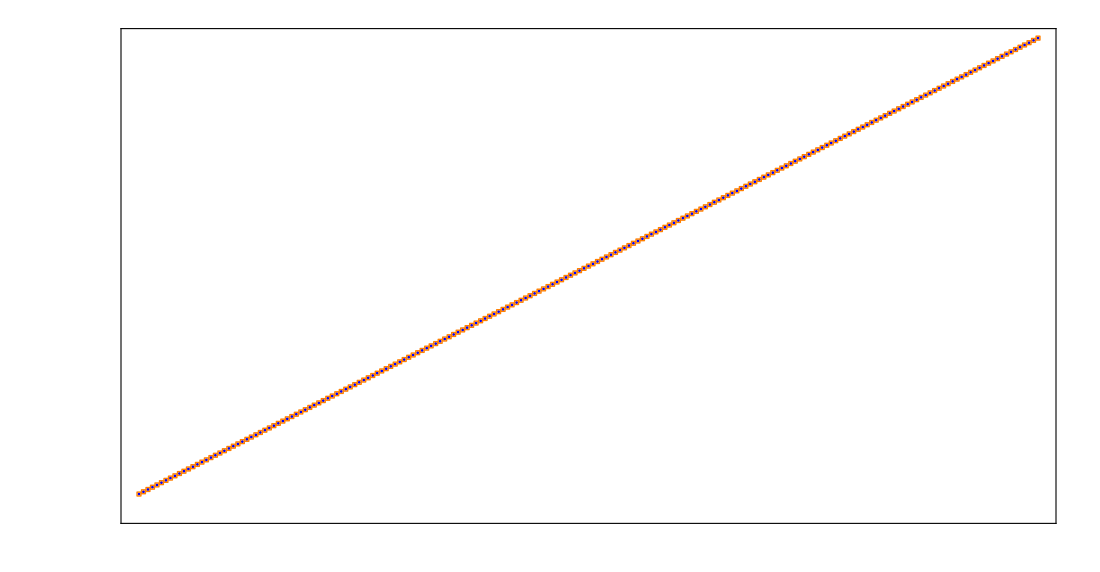
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
(* Refresh plotting settings without changing the computed Hamiltonians. *)
zzSettingsUsed=Join[zzSettingsUsed,KeyTake[zzSettings,{"PlotChop","MarkerSize"}]];
zzSpectrumPlots=edgePanels[zzData,zzGUsed,zzGroups,zzUsed,"ZZ","Energies","E_n(g)",
 "\\text{ZZ edge coupling: sector spectra}",zzSettingsUsed["PlotChop"],Lookup[zzSettingsUsed,"MarkerSize",3]];
zzSpectrumPlots[[1]]
```

### 10.7 Half-chain eigenvector entropy versus g

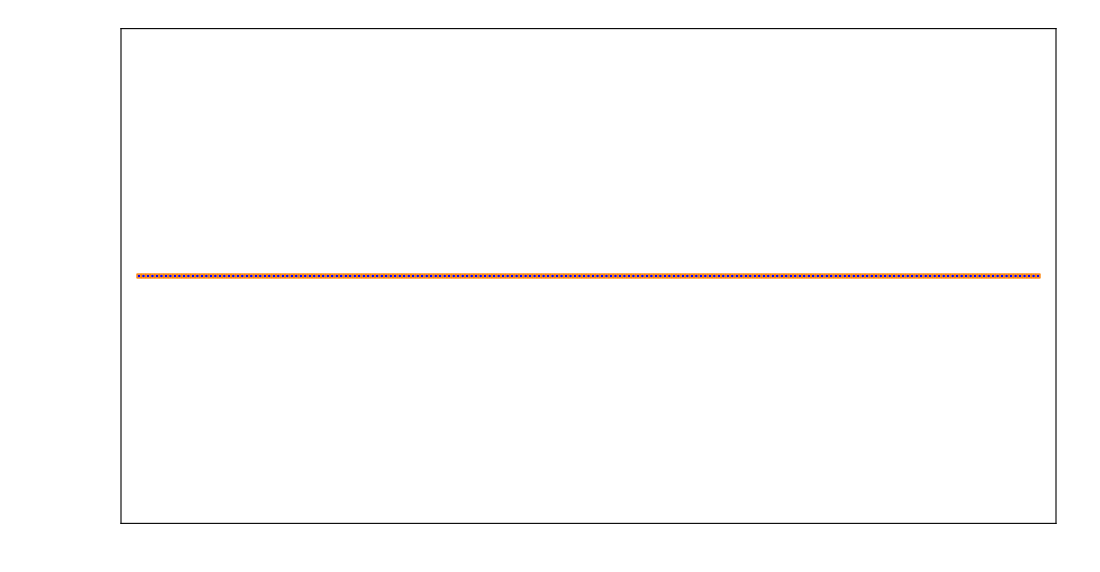
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
zzHalfPlots=edgePanels[zzData,zzGUsed,zzGroups,zzUsed,"ZZ","HalfEntropy",
 "S_{\\rm half}\\;(\\mathrm{nats})","\\text{ZZ edge coupling: half-chain entanglement}",
 zzSettingsUsed["PlotChop"],Lookup[zzSettingsUsed,"MarkerSize",3]];
zzHalfPlots[[1]]
```

### 10.8 Edges-versus-bulk eigenvector entropy versus g

```mathematica
zzEdgePlots=edgePanels[zzData,zzGUsed,zzGroups,zzUsed,"ZZ","EdgesEntropy",
 "S_{AB|\\rm bulk}\\;(\\mathrm{nats})","\\text{ZZ edge coupling: edges versus bulk}",
 zzSettingsUsed["PlotChop"],Lookup[zzSettingsUsed,"MarkerSize",3]];
zzEdgePlots[[1]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### 10.9 Computational-basis eigenvector IPR versus g

```mathematica
zzIPRPlots=edgePanels[zzData,zzGUsed,zzGroups,zzUsed,"ZZ","IPR",
 "\\mathrm{IPR}_{\\rm comp}","\\text{ZZ edge coupling: computational-basis IPR}",
 zzSettingsUsed["PlotChop"],Lookup[zzSettingsUsed,"MarkerSize",3]];
zzIPRPlots[[1]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### 10.10 Export the four plot families and scalar eigenstate data

```mathematica
zzDir=newFolder[zzOutputRoot,zzRunLabel<>"_L"<>ToString[zzUsed["L"]]<>
 "_J"<>safeToken[zzUsed["J"]]<>"_Delta"<>safeToken[zzUsed["Delta"]]];
edgeSave[zzDir,zzUsed,"ZZ",zzGUsed,zzGroups,zzResults,
 {{"spectrum",zzSpectrumPlots},{"half_entropy",zzHalfPlots},
  {"edge_bulk_entropy",zzEdgePlots},{"ipr",zzIPRPlots}},zzSettingsUsed];
```

Saved: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_edge_coupling_results\ZZ_L10_J1_Delta2

To inspect a full eigenket at one g without rerunning the sweep: zzOneED=zzEdgeED[1/10,zzUsed,zzSettingsUsed["EDTolerance"]]; then use the unchanged sectorTable[zzOneED] and eigenket[zzOneED,sector,level]. Rerun 10.4 onward for a new parameter set; no kernel reset is needed. Every spectrum, entropy, and IPR plot uses Joined->False and all supplied g values. The g-axis ticks are readable axis labels, not a second sampling grid. MarkerSize defaults to 3 points in zzSettings; open partner markers are slightly larger. For a style-only update, reevaluate the shared definitions in 10.2 and the plot/export cells with the retained data. Changing zzGGrid requires recomputing 10.5. Matching spectra do not impose matching eigenstate observables.

### 10.10a Export the additional ZZ audit and endpoint diagnostics

```mathematica
check[StringQ[Export[FileNameJoin[{zzDir,"sector_audit.wxf"}],
 <|"Model"->zzUsed,"gGrid"->zzGUsed,"SetupAudit"->zzSetupAudit,
  "BlockReductionAudit"->zzBlockAudit,"PointAudits"->zzAuditTable,
  "EndpointReports"->Lookup[zzResults,"EndpointReport"]|>,"WXF"]],
 "ZZ sector-audit export failed."];
```

## 11. Weak exchange-only coupling of the two edge spins: eigenstate g sweep

### 11.1 Model and remaining symmetry sectors

Here exchange ONLY means the XY (flip-flop) term, with no ZZ interaction on either edge bond:
H_exchange(g)=H_bulk+g(S_1^x S_2^x+S_1^y S_2^y+S_(L-1)^x S_L^x+S_(L-1)^y S_L^y).
NOTE ON THE USUAL LADDER-OPERATOR EXCHANGE: sigma^+=(sigma^x+i sigma^y)/2={{0,1},{0,0}}, sigma^-=(sigma^x-i sigma^y)/2={{0,0},{1,0}}. They equal S^+=S^x+i S^y and S^-=S^x-i S^y with the original S=sigma/2 convention. Thus S_i^x S_j^x+S_i^y S_j^y=(sigma_i^+ sigma_j^-+sigma_i^- sigma_j^+)/2. The edge interaction in this chapter is exactly (g/2)(sigma_1^+ sigma_2^-+sigma_1^- sigma_2^+ + sigma_(L-1)^+ sigma_L^-+sigma_(L-1)^- sigma_L^+). The matrix element |up,down> <-> |down,up> is g/2. If a different paper writes lambda(sigma_i^+ sigma_j^-+sigma_i^- sigma_j^+), its lambda equals g/2 here. The code retains the original spin-operator convention rather than silently changing the normalization of g.
H_bulk, S=sigma/2, the meaning of g, and zero fields are the same as in 10.1. This is an edge XY exchange, not a full Heisenberg or full XXZ edge bond. The two original XXZ edge bonds are again replaced.
For g!=0 the individual edge S^z values and the bulk magnetization are no longer conserved. Total magnetization M=Sum_i S_i^z remains conserved. Equal edge couplings preserve reflection R, and zero fields preserve global spin flip F. R and F commute, but F maps m to -m, so the simultaneously resolved labels are (m,r) for m!=0 and (m=0,r,f) for m=0. Each r,f is +/-1. A magnetization block has dimension Binomial[L,L/2-m] before reflection/spin-flip splitting. F gives equal-spectrum opposite-m partners rather than another label inside a nonzero-m block.
No full-chain S^2 label is used at Delta=+/-1 because the edge XY anisotropy breaks that symmetry. At g=0 the edges decouple and compatible extra edge/bulk charges are automatically resolved as in 10.2; the parent (m,r,f) labels remain fixed for the sweep. Since exactly degenerate states can be chosen in different eigenbases, endpoint entropies and IPR are not unique without this symmetry choice. In particular, F-resolved states at g=0 can be superpositions involving different edge magnetizations. For Delta=0 the entire model is an inhomogeneous XX chain with a free-fermion description; this is an additional special integrable limit, not a reason to assume the two interacting models have identical generic sectors.
The two chapters have independent parameters, results, plotting arrays, and output folders. To run chapter 11 alone, evaluate original definitions 1-2 and shared definitions 10.2 and audit definitions 10.3a, then 11.2 onward. The ZZ sweep is not required.

### 11.2 Exchange Hamiltonian and magnetization/reflection sectors

```mathematica
ClearAll[exEdgeH,exEdgeSpaces,exEdgeSetup,exEdgeED];
exEdgeH[g_,p_Association] := Module[{b=edgeBonds[edgeModel[p]]},
 check[realQ[g],"g must be finite and real."];SparseArray[b["Bulk"]+g b["Exchange"]]
];
exEdgeSpaces[p_,tol_] := Module[{l=p["L"],bits,q,ids,m,names,spaces,out={}},
 bits=Table[IntegerDigits[k,2,l],{k,0,2^l-1}];q=KeyTake[charges[p],{"R","F"}];
 Do[m=l/2-nDown;ids=Select[Range[2^l],Total[bits[[#]]]==nDown&];
  names=If[m==0,{"R","F"},{"R"}];
  spaces={<|"Basis"->IdentityMatrix[Length[ids]],"Labels"-><|"m"->m|>|>};
  Do[spaces=Flatten[splitCharge[#,N[Normal[q[name][[ids,ids]]]],name,tol]& /@ spaces,1],
   {name,names}];out=Join[out,Join[#,<|"Indices"->ids|>]& /@ spaces],{nDown,0,l}];out
];
exEdgeSetup[p_,tol_:10^-10] := edgeSetup[p,"Exchange",exEdgeSpaces,tol];
exEdgeED[g_,p_Association,tol_:10^-10] := edgeED[g,exEdgeSetup[p,tol],tol];
```

### 11.3 Editable exchange sweep parameters

```mathematica
exModel=<|"L"->10,"J"->1,"Delta"->2.|>;
exGGrid=N[Subdivide[0,1,200]];   (* g multiplies SxSx+SySy; the ladder coefficient is g/2. *)
exSettings=<|"EDTolerance"->10^-10,"MatchingTolerance"->10^-8,"PlotChop"->10^-10,"MarkerSize"->3|>;
exParallel=<|"Enabled"->True,"Kernels"->12|>;
exOutputRoot=FileNameJoin[{baseFolder[],"xxz_edge_coupling_results"}];
exRunLabel="Exchange";
```

### 11.4 Compute all eigenpairs, both entropies, and IPR at every g

```mathematica
exUsed=edgeModel[exModel];exGUsed=exGGrid;exSettingsUsed=exSettings;exParallelUsed=exParallel;
check[Length[exGUsed]>=2 && AllTrue[exGUsed,realQ] &&
 And@@Thread[Differences[N[exGUsed]]>0],"Exchange g grid must be real and strictly increasing."];
exSetup=exEdgeSetup[exUsed,exSettingsUsed["EDTolerance"]];
exSetupAudit=edgeSetupAudit[exSetup,exSettingsUsed["EDTolerance"]];
{exSeconds,exResults}=AbsoluteTiming[
 edgeCheckedSweep[exGUsed,exSetup,exSettingsUsed["EDTolerance"],exParallelUsed]];
exData=Lookup[exResults,"Data"];
exKeys=edgeSweepCheck[exResults,exGUsed,exUsed];
exGroups=Gather[exKeys,sameSpectrum[#1,#2,exData,exSettingsUsed["MatchingTolerance"]]&];
Print["Exchange sweep seconds: ",exSeconds,"; parent sectors: ",Length[exKeys],
 "; plotted groups: ",Length[exGroups]];
Dataset[First[exResults]["SectorTable"]]
```

Available parallel kernels: 12

Exchange sweep seconds: 48.114; parent sectors: 22; plotted groups: 13

### 11.5 Spectrum versus g

```mathematica
(* Refresh plotting settings without changing the computed Hamiltonians. *)
exSettingsUsed=Join[exSettingsUsed,KeyTake[exSettings,{"PlotChop","MarkerSize"}]];
exSpectrumPlots=edgePanels[exData,exGUsed,exGroups,exUsed,"Exchange","Energies","E_n(g)",
 "\\text{Exchange edge coupling: sector spectra}",exSettingsUsed["PlotChop"],Lookup[exSettingsUsed,"MarkerSize",3]];
exSpectrumPlots[[1]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### 11.6 Half-chain eigenvector entropy versus g

```mathematica
exHalfPlots=edgePanels[exData,exGUsed,exGroups,exUsed,"Exchange","HalfEntropy",
 "S_{\\rm half}\\;(\\mathrm{nats})","\\text{Exchange edge coupling: half-chain entanglement}",
 exSettingsUsed["PlotChop"],Lookup[exSettingsUsed,"MarkerSize",3]];
exHalfPlots[[1]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### 11.7 Edges-versus-bulk eigenvector entropy versus g

```mathematica
exEdgePlots=edgePanels[exData,exGUsed,exGroups,exUsed,"Exchange","EdgesEntropy",
 "S_{AB|\\rm bulk}\\;(\\mathrm{nats})","\\text{Exchange edge coupling: edges versus bulk}",
 exSettingsUsed["PlotChop"],Lookup[exSettingsUsed,"MarkerSize",3]];
exEdgePlots[[1]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### 11.8 Computational-basis eigenvector IPR versus g

```mathematica
exIPRPlots=edgePanels[exData,exGUsed,exGroups,exUsed,"Exchange","IPR",
 "\\mathrm{IPR}_{\\rm comp}","\\text{Exchange edge coupling: computational-basis IPR}",
 exSettingsUsed["PlotChop"],Lookup[exSettingsUsed,"MarkerSize",3]];
exIPRPlots[[1]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### 11.9 Export the four plot families and scalar eigenstate data

```mathematica
exDir=newFolder[exOutputRoot,exRunLabel<>"_L"<>ToString[exUsed["L"]]<>
 "_J"<>safeToken[exUsed["J"]]<>"_Delta"<>safeToken[exUsed["Delta"]]];
edgeSave[exDir,exUsed,"Exchange",exGUsed,exGroups,exResults,
 {{"spectrum",exSpectrumPlots},{"half_entropy",exHalfPlots},
  {"edge_bulk_entropy",exEdgePlots},{"ipr",exIPRPlots}},exSettingsUsed];
```

Saved: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_edge_coupling_results\Exchange_L10_J1_Delta2

Inspect one full eigensystem with exOneED=exEdgeED[1/10,exUsed,exSettingsUsed["EDTolerance"]], followed by sectorTable[exOneED] and eigenket[exOneED,sector,level]. Rerun 11.3 onward to change parameters. Each figure states the actual L,J,Delta, the edge interaction, the g range and step, zero fields, and sector dimensions. All four plot families use Joined->False, with MarkerSize defaulting to 3 points in exSettings. No plotting resampling is performed. For retained data, reevaluate 10.2 and the plot/export cells to apply these style changes; a new exGGrid requires recomputing 11.4. Data exports contain all eigenvalues and scalar eigenstate observables, all sector labels/dimensions, tolerances, and endpoint refinements. They do not retain eigenvectors at every g.

### 11.10 Inspect and export the exchange audit

```mathematica
exAuditTable=Lookup[exResults,"Audit"];
Dataset[exAuditTable]
```

```mathematica
check[StringQ[Export[FileNameJoin[{exDir,"sector_audit.wxf"}],
 <|"Model"->exUsed,"gGrid"->exGUsed,"SetupAudit"->exSetupAudit,
  "PointAudits"->exAuditTable,"EndpointReports"->Lookup[exResults,"EndpointReport"]|>,"WXF"]],
 "Exchange audit export failed."];
```

## 12. Exchange model: compare g, Delta and L using resolved spectral statistics

This chapter adds the comparison proposal that was previously missing from the .m file. The coupling scales below are distinct from each other. The gap-ratio cells can analyze the existing exchange sweep without rediagonalizing it. They do not automatically perform the proposed multi-size scan or establish a fitted crossover law.
Write H(g)=H0+gV, where H0 is the middle XXZ chain and two free edge spins, and V=edgeBonds[exUsed]["Exchange"] is dimensionless. Each edge bond has norm |g|/2 in the S=sigma/2 convention; the two-bond perturbation has norm at most |g|. For Delta=0 the full exchange model is a free-fermion chain for all g. For interacting Delta, generic boundary exchange can break integrability, but remaining symmetries must first be resolved and exceptional points must be checked. The absence of a paper's tuning relations alone is not a proof of nonintegrability.

### 12.1 Three comparisons; no single ratio diagnoses chaos

(1) Microscopic comparison: lambda=|g|/|J|. This compares the edge exchange coefficient with the transverse bulk exchange coefficient. The actual edge flip-flop matrix element is g/2, and the longitudinal bulk coefficient is J Delta. Keep Delta and the sign of J explicit when comparing different runs.
(2) Nearby-level hybridization: Lambda_nm=|g <n|V|m>|/|E_n^(0)-E_m^(0)|, within the same compatible symmetry sector and spectral window. Both the matrix elements and the spacings depend on L and Delta. A window-averaged |g| v_typ/d_typ can summarize this after defining how the matrix-element and spacing samples are selected. Comparing g with the mean level spacing alone neglects selection rules and matrix-element size. At g=0, first diagonalize V inside each exactly degenerate H0 manifold; never divide by a zero spacing. If an uncoupled pair has a vanishing matrix element, its small spacing does not imply hybridization.
(3) Low-energy comparison: kappa=|g|/epsilon_op(L,Delta), where epsilon_op is a positive bulk excitation energy accessible from the chosen low-energy state through the boundary operators S_2^+/- or S_(L-1)^+/-. Treat any degenerate ground manifold separately. In the gapless bulk the finite-size low-energy scales are typically of order v(Delta)/(L-2), with corrections; in the gapped bulk accessible bulk excitations can retain a finite scale. Boundary modes and nearly degenerate vacua must not be substituted automatically for the bulk gap. This low-energy comparison addresses boundary response and differs from spectral mixing in the central many-body band.

### 12.2 Concrete finite-size spectral comparison

Proposal: for antiferromagnetic J>0, compare L={8,10,12}, extending to L=14 when feasible, and Delta={0,0.5,1,1.5,3}. Use a common dimensionless lambda grid, initially logarithmic over positive lambda, with an explicitly separate g=0 endpoint. Refine the grid where the statistics change; no interpolation is needed to display the measured samples.
For even L, use (m=0,R=+1,F=+1) as the primary sector and analyze other sectors independently as checks. Its dimension is only 23 at L=8, so that size is indicative. Never pool equal-spectrum partners or sectors with different parities. Start with the middle 50 percent of ranks in each sector and record the actual level and ratio counts. This rank window is an operational convention, not an identical energy density across all L and Delta; check an energy-density window if a quantitative size collapse is pursued.
Compute delta_n=E_(n+1)-E_n and rtilde_n=Min[delta_n,delta_(n+1)]/Max[delta_n,delta_(n+1)] from unchopped energies. The reference means are 2 Log[2]-1=0.386294... for Poisson and approximately 0.5307 for a large GOE ensemble; the GOE three-level surmise gives a slightly different 0.5359. No unfolding is required for this ratio. Reference [2]: Y. Y. Atas et al., Phys. Rev. Lett. 110, 084101 (2013): https://arxiv.org/abs/1212.5611 .
Plot mean rtilde versus g/|J| separately for each L,Delta. If the data support a crossover, a crossing of the midpoint (0.3863+0.5307)/2=0.4585 can be reported descriptively only after checking size, window, gap resolution and uncertainty stability. A raw first crossing on a dense correlated g grid is not a reliable crossover estimator. Do not assume monotonicity or fit a size exponent before observing the curves. Boundary-only perturbations need not follow scaling laws derived for extensive bulk perturbations.
Controls: exchange at Delta=0, and the integrable ZZ model in separately resolved actual sectors. Integrability does not guarantee Poisson statistics for very small sectors or spectra with extra degeneracies. The g=0 free-edge spectrum requires endpoint refinements. For any unresolved or zero gap, report it; do not silently remove levels.
Reference [3] for the motivating boundary-impurity setting: P. Kattel et al., Edge modes and boundary impurities in the anisotropic Heisenberg spin chain, section V and appendix C: https://arxiv.org/abs/2412.00194 . Its nonintegrable study motivates comparison; it is not a direct verification of our XY-only two-edge path or its finite-size crossover.

### 12.3 Gap-ratio definitions using retained exchange data

The following functions keep every input energy, use a tolerance only to FLAG unresolved gaps, and return Missing for the sector mean if any gap pair in the chosen window is unresolved. Counts and individual ratio entries are retained. At g=0, exGapRows returns a separate DecoupledEndpoint status because the stored parent energies recombine extra symmetry sectors. The plotting helper omits Missing means, states the number of omitted samples, and leaves every status in the diagnostics table. It never joins points. These cells require the unchanged plotting definitions from section 2.

```mathematica
ClearAll[exGapRatios,exGapRows,exRatioPanel];
```

```mathematica
(* Raw levels only: no Chop, unfolding, or removal of degenerate levels. *)
exGapRatios[energies_List,window_:{1/4,3/4},tol_:10^-10] := Module[
 {e=Sort[N[energies]],d,lo,hi,w,gaps,cut,pairs,ratios,unresolved,status},
 check[AllTrue[e,realQ] && Length[window]==2 && 0<=window[[1]]<window[[2]]<=1 &&
  realQ[tol] && tol>0,"Invalid energy list, rank window, or gap tolerance."];
 d=Length[e];lo=Max[1,Floor[window[[1]] d]+1];hi=Min[d,Ceiling[window[[2]] d]];
 w=If[d>0 && hi>=lo,e[[lo;;hi]],{}];gaps=Differences[w];
 cut=tol Max[1.,maxAbs[e]];pairs=Partition[gaps,2,1];
 ratios=Map[If[Min[#]<=cut,Missing["UnresolvedGapPair"],Min[#]/Max[#]]&,pairs];
 unresolved=Count[ratios,_Missing];
 status=Which[Length[w]<3,"TooFewLevels",unresolved>0,"UnresolvedGaps",True,"OK"];
 <|"SectorDimension"->d,"WindowRanks"->{lo,hi},"WindowLevels"->Length[w],
  "GapPairs"->Length[pairs],"UnresolvedGapPairs"->unresolved,
  "UnresolvedGaps"->Count[gaps,x_/;x<=cut],"GapResolution"->cut,
  "Ratios"->ratios,"MeanR"->If[status=="OK",Mean[ratios],Missing[status]],
  "IIDSEM"->If[status=="OK" && Length[ratios]>=2,StandardDeviation[ratios]/Sqrt[Length[ratios]],Missing["Unavailable"]],
  "MeanSpacing"->If[Length[gaps]>0,Mean[gaps],Missing["NoGaps"]],"Status"->status|>
];
```

```mathematica
(* Keep opposite-m and parity partners separate, even if spectra coincide. *)
exGapRows[results_List,p_,window_:{1/4,3/4},tol_:10^-10] := Flatten[
 Map[Function[point,KeyValueMap[Function[{key,s},
   Join[<|"L"->p["L"],"J"->p["J"],"Delta"->p["Delta"],
    "g"->point["g"],"gOverJ"->point["g"]/Abs[p["J"]],
    "SectorKey"->key,"Labels"->s["Labels"]|>,
    If[TrueQ[point["g"]==0],
     <|"SectorDimension"->s["Dimension"],"Status"->"DecoupledEndpoint",
      "MeanR"->Missing["EndpointParentRecombinesExtraSectors"],
      "Reason"->"At g=0 use independently refined sectors, not recombined parent energies."|>,
     exGapRatios[s["Energies"],window,tol]]]],point["Data"]]],results],1];
```

```mathematica
(* Small unjoined markers; benchmarks are labels, not joined reference curves. *)
exRatioPanel[rows_List,labels_Association,p_,window_:{1/4,3/4},marker_:3] := Module[
 {selected,valid,points,cap,g},
 (* Explicit label matching avoids any dependence on Association key order. *)
 selected=Select[rows,Function[row,And@@KeyValueMap[
   Lookup[row["Labels"],#1,Missing["Label"]]==#2&,labels]]];
 valid=Select[selected,NumericQ[#["MeanR"]]&];
 check[valid=!={},"This sector has no resolved gap-ratio values in the chosen window."];
 points=({#["gOverJ"],#["MeanR"]}& /@ valid);
 cap=Column[{caption[p,"\\Delta="<>texNumber[p["Delta"]]],
   tex["H_{\\rm edge}=g\\sum_{(i,j)\\in\\{(1,2),(L-1,L)\\}}(S_i^xS_j^x+S_i^yS_j^y)",13],
   tex[sectorLabel[labels]<>";\\quad d="<>ToString[First[selected]["SectorDimension"]]<>
    ";\\quad \\mathrm{rank\\ window}=["<>
    texNumber[window[[1]]]<>","<>texNumber[window[[2]]]<>"]",13],
   tex["\\langle\\tilde r\\rangle_{\\rm Poisson}=0.3863;\\quad "<>
    "\\langle\\tilde r\\rangle_{\\rm GOE}\\simeq0.5307",13],
   Style["Plotted "<>ToString[Length[valid]]<>" of "<>ToString[Length[selected]]<>
    " g samples. Excluded samples and reasons remain in the diagnostics table.",12]},Alignment->Center];
 g=Block[{plotChop=0},framePlot[{points},"g/|J|","\\langle\\tilde r\\rangle",
    {Blue},{},False,False,{{"●",marker}}]];
 plotPanel["\\text{Exchange: resolved-sector gap ratios}",cap,g]
];
```

### 12.4 Editable gap-ratio settings and sector selection

This selects an existing sector for display; it is not a largest-sector search. At the chapter-11 defaults L=10, Delta=0.5, this sector has D=71, 37 window levels and 35 ratios. IIDSEM is a descriptive independent-sample estimate; neighboring ratios and neighboring g samples are correlated. Use chapter 13 for independent larger-size target-sector scans.

```mathematica
exRatioSettings=<|"RankWindow"->{1/4,3/4},"GapResolution"->10^-10,"MarkerSize"->3|>;
exRatioSector=<|"m"->0,"R"->1,"F"->1|>;   (* Even L; use existing labels for odd L. *)
```

### 12.4.1 Density of states of the selected symmetry sector

```mathematica
(* 12.4a — Editable DOS settings *)
check[ValueQ[exResults] && ValueQ[exUsed] && ValueQ[exGUsed],
  "Run 11.4 or load its matching results first."];
(* Choose existing g samples. You can replace this with {0.1,0.5,1.}. *)
exDOSGValues = DeleteDuplicates[{
   First[exGUsed],
   exGUsed[[Ceiling[Length[exGUsed]/2]]],
   Last[exGUsed]
   }];
exDOSBins = 30;
exDOSNormalize = True;  (* True: integral 1; False: integral D. *)
exDOSOutputRoot =
  FileNameJoin[{baseFolder[], "xxz_edge_coupling_results"}];
exDOSRunLabel = "Exchange_DOS";
exDOSWindowUsed = exRatioSettings["RankWindow"];
exDOSSectorUsed = exRatioSector;
exDOSModelUsed = exUsed;
exDOSSettingsUsed = <|
   "Bins" -> exDOSBins,
   "Normalized" -> exDOSNormalize,
   "RankWindow" -> exDOSWindowUsed
   |>;
check[IntegerQ[exDOSBins] && exDOSBins >= 2 &&
   MemberQ[{True, False}, exDOSNormalize],
  "Invalid DOS settings."];
check[Length[exDOSWindowUsed] == 2 &&
   0 <= exDOSWindowUsed[[1]] < exDOSWindowUsed[[2]] <= 1,
  "Invalid RankWindow."];
```

```mathematica
(* 12.4b — Extract the chosen sector and plot its DOS *)
(* Energies from different g values are never pooled. *)
exDOSData = Table[
   Module[
    {point, sectors, e, d, lo, hi, span,
     edges, counts, heights, cdf},

    point = First[MinimalBy[exResults, Abs[#["g"] - g] &]];

    check[Abs[point["g"] - g] <= 10^-10 Max[1., Abs[g]],
     "A requested DOS g value is absent from exResults."];

    sectors = Select[Values[point["Data"]],
      Function[s, And @@ KeyValueMap[
         Lookup[s["Labels"], #1, Missing["Label"]] == #2 &,
         exDOSSectorUsed]]];

    check[Length[sectors] == 1,
     "DOS selection must identify exactly one sector. Check its labels."];

    e = Sort[N[First[sectors]["Energies"]]];
    d = Length[e];

    check[d > 0 && AllTrue[e, realQ], "Invalid sector energies."];

    (* Identical rank convention to exGapRatios. *)
    lo = Max[1, Floor[exDOSWindowUsed[[1]] d] + 1];
    hi = Min[d, Ceiling[exDOSWindowUsed[[2]] d]];

    (* Bins cover every energy, including both spectral endpoints. *)
    span = Max[
      Last[e] - First[e],
      10^-6 Max[1., maxAbs[e]]
      ];

    edges = Subdivide[
      First[e] - .02 span,
      Last[e] + .02 span,
      exDOSBins
      ];

    {edges, counts} = HistogramList[e, {edges}, "Count"];

    check[Total[counts] == d,
     "DOS bins failed to include every level."];

    heights =
     counts/Differences[edges]/If[exDOSNormalize, d, 1];

    (* Exact empirical cumulative DOS; repeated energies are retained. *)
    cdf = Join[
      {{First[edges], 0.}},
      Flatten[
       Table[
        {{e[[k]], (k - 1.)/d}, {e[[k]], k/d}},
        {k, d}
        ], 1],
      {{Last[edges], 1.}}
      ];

    <|
     "g" -> point["g"],
     "Labels" -> First[sectors]["Labels"],
     "Dimension" -> d,
     "Energies" -> e,
     "BinEdges" -> edges,
     "BinCounts" -> counts,
     "DOSHeights" -> heights,
     "Normalized" -> exDOSNormalize,
     "CDFPoints" -> cdf,
     "RankWindow" -> exDOSWindowUsed,
     "WindowRanks" -> {lo, hi},
     "WindowLevels" -> hi - lo + 1,
     "WindowEnergies" -> e[[{lo, hi}]]
     |>
    ],
   {g, exDOSGValues}
   ];

Print[Dataset[
  KeyTake[#, {
      "g", "Labels", "Dimension",
      "WindowRanks", "WindowLevels", "WindowEnergies"
      }] & /@ exDOSData
  ]];


ClearAll[exDOSFigure];
exDOSFigure[r_, cumulative_: False] := Module[
  {edges = r["BinEdges"], h = r["DOSHeights"],
   yMax, primitives, eLeft, eRight, cap, graph, ylabel},

  {eLeft, eRight} = r["WindowEnergies"];
  yMax = If[cumulative, 1., 1.1 Max[h]];

  primitives = If[cumulative,
    {Directive[Blue, AbsoluteThickness[1.7]],
     Line[r["CDFPoints"]]},
    {Directive[Blue, Opacity[.55]],
     MapThread[
      Rectangle[{#1, 0}, {#2, #3}] &,
      {Most[edges], Rest[edges], h}
      ]}
    ];

  ylabel = If[cumulative,
    "N(E)/D",
    If[r["Normalized"], "\\rho(E)/D", "\\rho(E)"]
    ];

  cap = Column[{
      tex[
       "L=" <> texNumber[exDOSModelUsed["L"]] <>
        ",\\quad J=" <> texNumber[exDOSModelUsed["J"]] <>
        ",\\quad \\Delta=" <>
        texNumber[exDOSModelUsed["Delta"]] <>
        ",\\quad g=" <> texNumber[r["g"]], 13],

      tex[
       sectorLabel[r["Labels"]] <>
        ";\\quad D=" <> ToString[r["Dimension"]], 13],

      Style[
       "Equal XY end bonds; zero fields. Orange region: ranks " <>
        ToString[r["WindowRanks"][[1]]] <> "–" <>
        ToString[r["WindowRanks"][[2]]] <> " (" <>
        ToString[r["WindowLevels"]] <> " levels).", 12]
      },
    Alignment -> Center
    ];

  graph = Graphics[primitives,
    Epilog -> {
      Directive[Orange, Opacity[.12]],
      Rectangle[{eLeft, 0}, {eRight, yMax}],

      Directive[Orange, Opacity[1], Dashed,
       AbsoluteThickness[1.5]],
      Line[{{eLeft, 0}, {eLeft, yMax}}],
      Line[{{eRight, 0}, {eRight, yMax}}]
      },
    Frame -> True,
    Axes -> False,
    FrameLabel -> {tex["E", 19], tex[ylabel, 19]},
    FrameTicks -> {
      {ticks[0, yMax], None},
      {ticks[First[edges], Last[edges]], None}
      },
    PlotRange -> {{First[edges], Last[edges]}, {0, yMax}},
    PlotRangePadding -> None,
    Background -> White,
    ImageSize -> 900,
    ImagePadding -> {{110, 30}, {75, 35}}
    ];

  plotPanel[
   If[cumulative,
    "\\text{Cumulative DOS}",
    "\\text{Selected-sector DOS}"],
   cap, graph
   ]
  ];
```

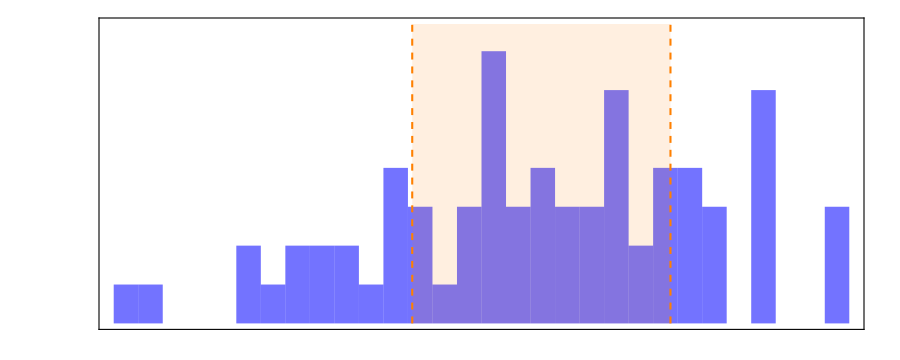
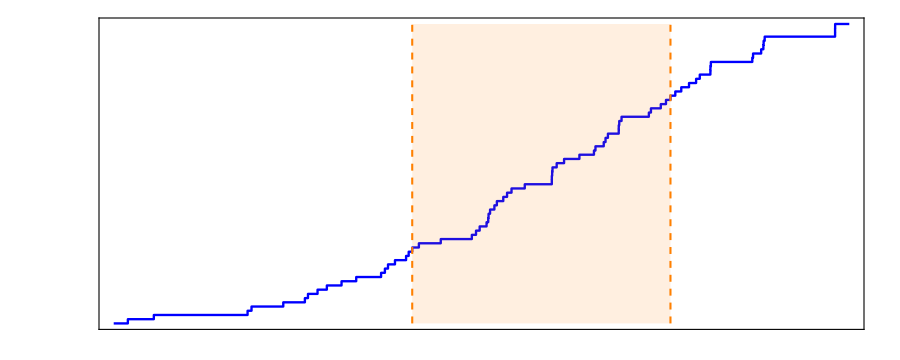
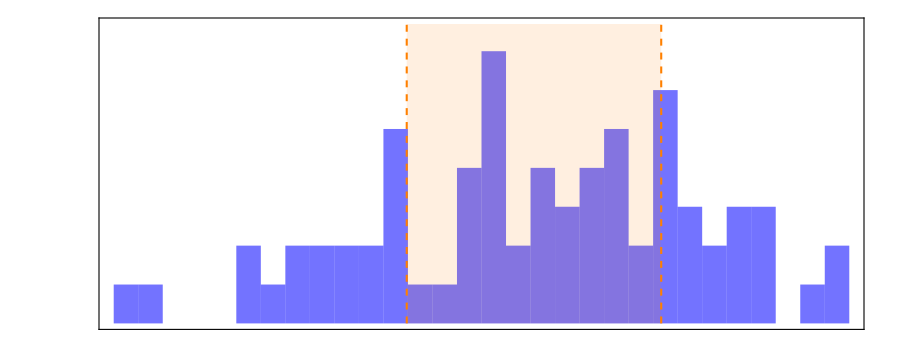
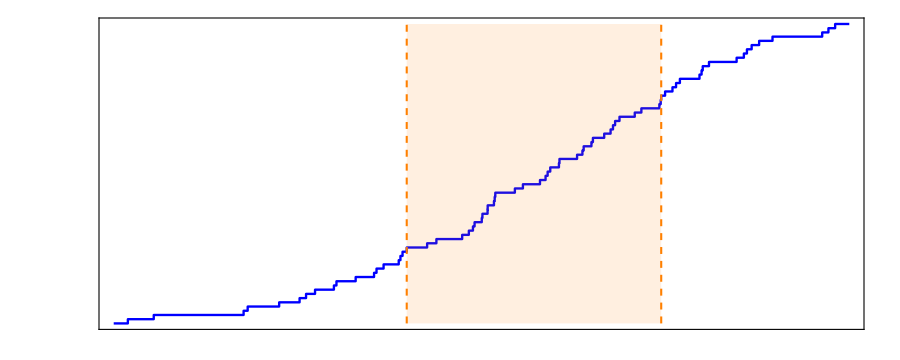
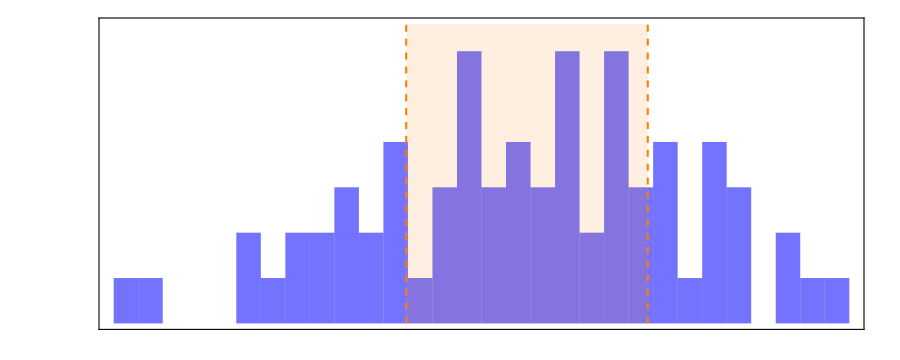
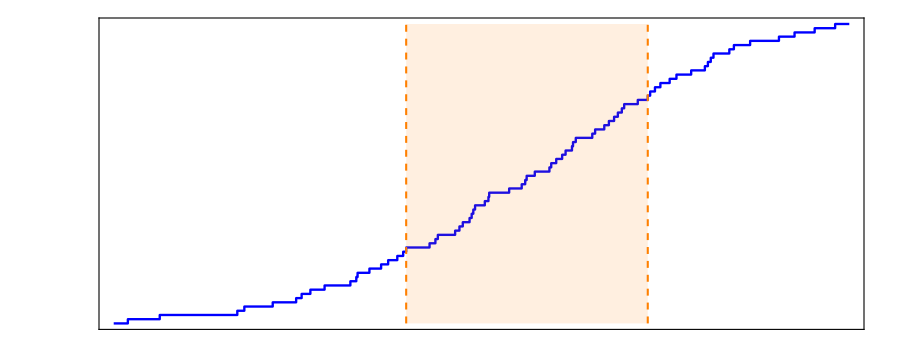
-Graphics-
-Graphics-
-Graphics-
Equal XY end bonds; zero fields. Orange region: ranks 18–54 (37 levels).
-Graphics-
-Graphics-
-Graphics-
-Graphics-
Equal XY end bonds; zero fields. Orange region: ranks 18–54 (37 levels).
-Graphics-
-Graphics-
-Graphics-
-Graphics-
Equal XY end bonds; zero fields. Orange region: ranks 18–54 (37 levels).
-Graphics-
-Graphics-
-Graphics-
-Graphics-
Equal XY end bonds; zero fields. Orange region: ranks 18–54 (37 levels).
-Graphics-
-Graphics-
-Graphics-
-Graphics-
Equal XY end bonds; zero fields. Orange region: ranks 18–54 (37 levels).
-Graphics-
-Graphics-
-Graphics-
-Graphics-
Equal XY end bonds; zero fields. Orange region: ranks 18–54 (37 levels).
-Graphics-

```mathematica
exDOSPlots = exDOSFigure /@ exDOSData;
exDOSCDFPlots = exDOSFigure[#, True] & /@ exDOSData;

Print[Column[
  MapThread[
   Column[{#1, #2}, Spacings -> 1] &,
   {exDOSPlots, exDOSCDFPlots}
   ],
  Spacings -> 2
  ]];
```

```mathematica
(* 12.4c — Export plots and raw DOS data *)
exDOSDir = newFolder[
   exDOSOutputRoot,
   exDOSRunLabel <>
    "_L" <> ToString[exDOSModelUsed["L"]] <>
    "_Delta" <> safeToken[exDOSModelUsed["Delta"]]
   ];

Do[
  savePNG[
   FileNameJoin[{exDOSDir,
     "dos_g_" <> safeToken[exDOSData[[k]]["g"]] <> ".png"}],
   exDOSPlots[[k]]
   ];

  savePNG[
   FileNameJoin[{exDOSDir,
     "cdf_g_" <> safeToken[exDOSData[[k]]["g"]] <> ".png"}],
   exDOSCDFPlots[[k]]
   ],
  {k, Length[exDOSData]}
  ];

check[StringQ[Export[
    FileNameJoin[{exDOSDir, "sector_dos.wxf"}],
    <|
     "Model" -> exDOSModelUsed,
     "SelectedSector" -> exDOSSectorUsed,
     "Settings" -> exDOSSettingsUsed,
     "Results" -> exDOSData
     |>,
    "WXF"
    ]],
  "DOS data export failed."];
Print["DOS plots and data saved to: ", exDOSDir];
```

DOS plots and data saved to: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_edge_coupling_results\Exchange_DOS_L10_Delta2

### 12.5 Compute and inspect gap-ratio diagnostics; reuse exResults

```mathematica
check[ValueQ[exResults] && ValueQ[exUsed],"Run 11.4 or load its matching results and parameters first."];
exRatioSettingsUsed=exRatioSettings;exRatioSectorUsed=exRatioSector;
exGapReport=exGapRows[exResults,exUsed,exRatioSettingsUsed["RankWindow"],
 exRatioSettingsUsed["GapResolution"]];
exGapSelected=Select[exGapReport,Function[row,And@@KeyValueMap[
 Lookup[row["Labels"],#1,Missing["Label"]]==#2&,exRatioSectorUsed]]];
check[exGapSelected=!={},"The selected sector does not exist; inspect the labels in exGapReport."];
Dataset[KeyDrop[#, {"Ratios"}]& /@ exGapSelected]
```

### 12.6 Mean adjacent-gap ratio versus g/|J|; small unjoined points

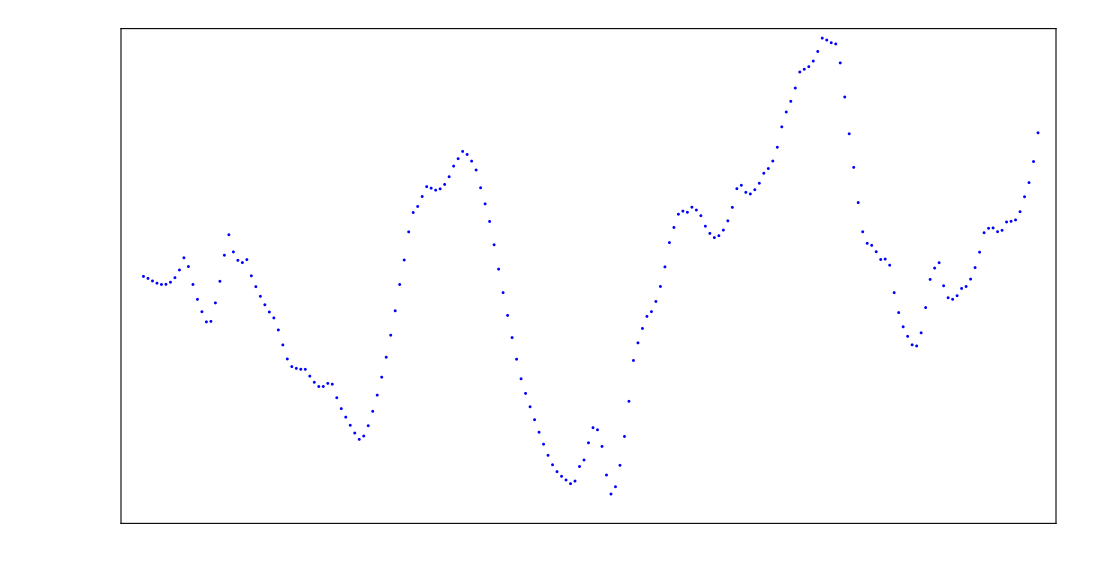
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
Plotted 200 of 201 g samples. Excluded samples and reasons remain in the diagnostics table.
-Graphics-

```mathematica
exGapPlot=exRatioPanel[exGapReport,exRatioSectorUsed,exUsed,
 exRatioSettingsUsed["RankWindow"],exRatioSettingsUsed["MarkerSize"]];
exGapPlot
```

### 12.7 Export gap ratios and diagnostics alongside the exchange sweep

```mathematica
exDir
```

C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_edge_coupling_results\Exchange_L10_J1_Delta2

```mathematica
check[ValueQ[exDir] && DirectoryQ[exDir],"Evaluate 11.9 to create the exchange output folder first."];
savePNG[FileNameJoin[{exDir,"gap_ratios.png"}],exGapPlot];
check[StringQ[Export[FileNameJoin[{exDir,"gap_ratios.wxf"}],
 <|"Model"->exUsed,"gGrid"->exGUsed,"Settings"->exRatioSettingsUsed,
  "SelectedSector"->exRatioSectorUsed,"Results"->exGapReport|>,"WXF"]],
 "Gap-ratio data export failed."];
```

To compare sizes or anisotropies, rerun 11.3 onward with the desired parameters and retain each exported gap_ratios.wxf. Each record includes L,J,Delta,g,g/|J| and its actual sector labels. This chapter does not automatically launch a large L,Delta grid. To analyze a true independently resolved endpoint child at one g=0, obtain ed0=edgeCheckedED[0,exSetup,exSettingsUsed["EDTolerance"]] and apply exGapRatios to ed0["Sectors"][[k]]["Eigenvalues"] separately for each k. Missing means signal inadequate level counts or unresolved gaps; they are not numerical evidence for or against integrability.

## 13. Independent selected-sector gap ratios across system sizes

Run 13.2 once, then either 13.3 (linear g) or 13.4 (logarithmic g). No earlier definitions, Hamiltonians, diagonalizations, exResults, or exports are required. The two runs have separate editable configurations, results, plots and folders. In each configuration, Sector is near the top: Automatic selects the largest sector of the stated classification; replace it with an explicit association to analyze another sector. LValues, J, Delta, g limits and g-point count are all independent of earlier chapters.

### 13.1 Model, sector choice, dimensions and statistic

H=J Sum_(i=2)^(L-2) (S_i^x S_(i+1)^x+S_i^y S_(i+1)^y+Delta S_i^z S_(i+1)^z) + g(S_1^x S_2^x+S_1^y S_2^y+S_(L-1)^x S_L^x+S_(L-1)^y S_L^y), S=sigma/2. Both end bonds have the same g; there are no fields. The opposite-spin hopping amplitude is J/2 in the bulk and g/2 at either end.
Use (m,R) for nonzero m and (m=0,R,F) at zero m, with R,F=+/-1. F is the product of Pauli sigma-x matrices, independent of L-dependent rotation phases. Automatic chooses the largest block by exact character dimensions, breaking ties toward positive m then positive parity. For even L>=6 this gives m=1,R=+1 (opposite-m partners are not pooled); for odd L the largest block is m=1/2,R=+1. Run even and odd size families separately. The selected labels must agree across all L in one run.
For even L=10,12,14,16 the default dimensions are 110,396,1519,5720. The m=0,R=+1,F=+1 alternative has 71,252,890,3299. MinimumDimension=500 is enforced by default; lower it explicitly for small validation runs. All eigenvalues of the selected block are computed before taking the middle rank window; do not use a few extremal eigenvalues for central-band statistics.
The basis is generated from fixed-m spin configurations and R/F orbits. Only the selected basis and its three projected bond matrices are built. Character formulas count other sectors without constructing them. There is no full 2^L Hamiltonian, no ED of other sectors, and no eigenvector or entropy calculation. Basis orthogonality, invariance of every bond part and Hermiticity are checked before the scan. Dense full-spectrum ED still costs O(D^2) memory and roughly O(D^3) work per g; the basis construction also scales with Binomial[L,L/2-m]. Sizes run sequentially.
The common sectors remain invariant for all real Delta and g, but at g=0 they contain additional conserved edge/bulk quantities. Therefore that point has status DecoupledEndpoint and no reported mean. At Delta=0, free-fermion conserved quantities make this an integrable control, not a generic GOE sector. At Delta=+/-1 with g!=0 the XY-only edge bonds do not restore full-chain S^2. No claim of complete irreducibility at every exceptional parameter point is made.
For sorted selected-sector energies, delta_n=E_(n+1)-E_n and r_n=Min[delta_n,delta_(n+1)]/Max[delta_n,delta_(n+1)]. Ranks are floor(a D)+1 through ceil(b D), clipped to the spectrum. GapResolution times Max[1,max |E|] flags unresolved gaps. No levels are removed and any unresolved pair makes MeanR Missing. The unaltered energies may be retained with StoreEnergies=True. WorkingPrecision can be increased, using exact/high-precision parameters; machine decimals are rejected for an arbitrary-precision run.
IIDSEM=sample standard deviation/Sqrt[number of ratios] assumes independent samples. BlockSEM uses nonoverlapping blocks of consecutive ratios and requires at least four blocks; its final incomplete block is omitted only from this uncertainty estimate, with the count recorded. MeanR always uses all resolved ratios. Neither estimate is a calibrated confidence interval for this deterministic spectrum. Vary BlockLength, rank window and L; do not infer a crossover from a noisy first crossing. Ratios at nearby g are correlated and are not extra independent samples.

### 13.2 Standalone definitions: basis, spectra, statistics, plots and export

```mathematica
(* Standalone chapter-13 definitions. No earlier chapters or results are required. *)
ClearAll[sgCheck,sgRealQ,sgMax,sgDimension,sgCatalog,sgLabels,sgBasis,
 sgAction,sgSetup,sgStatistics,sgPoint,sgGrid,sgValidate,sgScan,
 sgPlot,sgExport,sgBaseFolder];
sgCheck[test_,message_] := If[!TrueQ[test],Print[Style[message,Red]];Abort[]];
sgRealQ[x_] := NumericQ[x] && NumberQ[N[x]] && TrueQ[Im[N[x]]==0];
sgMax[x_] := If[Head[x]===SparseArray,Max[0,Sequence@@Abs[x["NonzeroValues"]]],
 Max[0,Sequence@@Abs[Flatten[{x}]]]];
```

```mathematica
(* Character traces give dimensions without constructing other sector bases. *)
sgDimension[l_Integer,lab_Association] := Module[{n=l/2-lab["m"],trR,d},
 If[!IntegerQ[n] || n<0 || n>l,Return[0]];
 d=Binomial[l,n];
 trR=If[EvenQ[l],If[EvenQ[n],Binomial[l/2,n/2],0],
   Binomial[(l-1)/2,Floor[n/2]]];
 If[n==l/2,(d+lab["R"] trR+lab["R"] lab["F"] 2^(l/2))/4,
   (d+lab["R"] trR)/2]
];
sgCatalog[l_Integer] := Module[{labs,rows},
 labs=Flatten[Table[If[2 n==l,
   Flatten[Table[<|"m"->0,"R"->r,"F"->f|>,{r,{1,-1}},{f,{1,-1}}]],
   Table[<|"m"->l/2-n,"R"->r|>,{r,{1,-1}}]],{n,0,l}]];
 rows=(<|"Labels"->#,"Dimension"->sgDimension[l,#]|>& /@ labs);
 SortBy[Select[rows,#["Dimension"]>0&],
  {-#["Dimension"],Abs[#["Labels"]["m"]],-#["Labels"]["m"],
    -#["Labels"]["R"],-Lookup[#["Labels"],"F",0]}&]
];
sgLabels[l_Integer,choice_] := Module[{lab=choice,n},
 If[choice===Automatic,lab=First[sgCatalog[l]]["Labels"]];
 sgCheck[AssociationQ[lab] && KeyExistsQ[lab,"m"] && KeyExistsQ[lab,"R"],
  "Sector must be Automatic or an association containing m and R."];
 n=l/2-lab["m"];
 sgCheck[IntegerQ[n] && 0<=n<=l && MemberQ[{-1,1},lab["R"]],
  "Use an exact allowed integer/half-integer m, and R=+1 or -1."];
 sgCheck[Sort[Keys[lab]]===Sort[If[lab["m"]==0,{"m","R","F"},{"m","R"}]],
  "Use exactly m,R,F at m=0; exactly m,R at nonzero m. F maps m to -m."];
 If[lab["m"]==0,sgCheck[MemberQ[{-1,1},lab["F"]],"F must be +1 or -1."]];
 sgCheck[sgDimension[l,lab]>0,"This symmetry sector is empty at the requested L."];
 KeySort[lab]
];
```

```mathematica
(* Enumerate only fixed-m bit strings. Each symmetry orbit contributes at most one column. *)
sgBasis[l_Integer,lab_Association,wp_] := Module[
 {n=l/2-lab["m"],states,index,seen,bRules={},cols=0,x,rx,orbit,signs,
  weights,rows,vals,nn,b,dim=sgDimension[l,lab],r=lab["R"],f},
 states=Sort[Total /@ Subsets[2^Range[0,l-1],{n}]];
 index=AssociationThread[states,Range[Length[states]]];
 seen=ConstantArray[False,Length[states]];
 Do[If[seen[[index[x]]],Continue[]];
  rx=FromDigits[Reverse[IntegerDigits[x,2,l]],2];
  If[lab["m"]==0,f=lab["F"];orbit={x,rx,2^l-1-x,2^l-1-rx};signs={1,r,f,r f},
    orbit={x,rx};signs={1,r}];
  seen[[Lookup[index,DeleteDuplicates[orbit]]]]=True;
  weights=Select[Merge[MapThread[Rule,{orbit,signs}],Total],#!=0&];
  If[Length[weights]==0,Continue[]];cols++;
  rows=Lookup[index,Keys[weights]];vals=Values[weights];nn=Sqrt[Total[vals^2]];
  bRules=Join[bRules,MapThread[{#1,cols}->#2&,{rows,N[vals/nn,wp]}]],{x,states}];
 sgCheck[cols==dim,"Orbit count does not agree with the character dimension."];
 b=SparseArray[bRules,{Length[states],dim}];
 <|"L"->l,"Labels"->lab,"States"->states,"Index"->index,"Basis"->b,
  "Dimension"->dim,"MagnetizationDimension"->Length[states]|>
];
```

```mathematica
(* Apply local bonds to the selected basis, without making a full Hamiltonian or other sectors. *)
sgAction[basis_,kind_,wp_] := Module[
 {l=basis["L"],states=basis["States"],index=basis["Index"],b=basis["Basis"],
  entries,terms,row,col,amp,x,bits,z,bonds,y,merged},
 entries=Most[ArrayRules[b]];
 bonds=If[kind=="EdgeXY",{1,l-1},Range[2,l-2]];
 terms=Reap[Do[row=entry[[1,1]];col=entry[[1,2]];amp=Last[entry];
   x=states[[row]];bits=IntegerDigits[x,2,l];
   If[kind=="BulkZZ",z=Total[Table[(1-2 bits[[j]])(1-2 bits[[j+1]])/4,{j,bonds}]];
     If[z!=0,Sow[{row,col}->amp z]],
     Do[If[bits[[j]]!=bits[[j+1]],y=BitXor[x,2^(l-j)+2^(l-j-1)];
       Sow[{index[y],col}->amp/2]],{j,bonds}]],{entry,entries}]][[2]];
 If[terms==={},Return[SparseArray[{},Dimensions[b]]]];
 merged=({First[#][[1]]->Total[Last /@ #]}& /@ GatherBy[First[terms],First]);
 N[SparseArray[Flatten[merged,1],Dimensions[b]],wp]
];
```

```mathematica
sgSetup[l_Integer,choice_,wp_:MachinePrecision,tol_:10^-10] := Module[
 {lab=sgLabels[l,choice],basis,b,parts=<||>,a,h,leak=0,herm=0,orth,scale},
 basis=sgBasis[l,lab,wp];b=basis["Basis"];
 orth=sgMax[ConjugateTranspose[b].b-SparseArray[Band[{1,1}]->1,{basis["Dimension"],basis["Dimension"]}]];
 Do[a=sgAction[basis,kind,wp];h=ConjugateTranspose[b].a;scale=Max[1,sgMax[a]];
  leak=Max[leak,sgMax[a-b.h]/scale];herm=Max[herm,sgMax[h-ConjugateTranspose[h]]/scale];
  AssociateTo[parts,kind->SparseArray[(h+ConjugateTranspose[h])/2]],
  {kind,{"BulkXY","BulkZZ","EdgeXY"}}];
 sgCheck[Max[orth,leak,herm]<tol,"Target-sector basis or invariance audit failed."];
 <|"L"->l,"Labels"->lab,"Dimension"->basis["Dimension"],
  "MagnetizationDimension"->basis["MagnetizationDimension"],"Parts"->parts,
  "WorkingPrecision"->wp,"Audit"-><|"BasisError"->orth,
   "RelativeSectorLeakage"->leak,"RelativeHermiticityError"->herm,"Passed"->True|>|>
];
```

```mathematica
(* Missing values retain degeneracies: do not deduplicate or Chop energies. *)
sgStatistics[energies_List,cfg_] := Module[
 {e=Sort[energies],d,lo,hi,w,gaps,pairs,cut,ratios,status,valid,n,blocks,bs,
  iid=Missing["Unavailable"],bse=Missing["TooFewBlocks"],nb=0,used=0},
 d=Length[e];{lo,hi}={Max[1,Floor[cfg["RankWindow"][[1]] d]+1],
   Min[d,Ceiling[cfg["RankWindow"][[2]] d]]};
 w=If[hi>=lo,e[[lo;;hi]],{}];gaps=Differences[w];pairs=Partition[gaps,2,1];
 cut=cfg["GapResolution"] Max[1,sgMax[e]];
 ratios=(If[Min[#]<=cut,Missing["UnresolvedGapPair"],Min[#]/Max[#]]& /@ pairs);
 n=Length[ratios];status=Which[Length[w]<3,"TooFewLevels",
   Count[ratios,_Missing]>0,"UnresolvedGaps",True,"OK"];
 If[status=="OK" && n>=2,iid=StandardDeviation[ratios]/Sqrt[n]];
 bs=cfg["BlockLength"];
 If[status=="OK",blocks=Partition[ratios,bs];nb=Length[blocks];used=nb bs;
   If[nb>=4,bse=StandardDeviation[Mean /@ blocks]/Sqrt[nb]]];
 <|"SectorDimension"->d,"WindowRanks"->{lo,hi},"WindowLevels"->Length[w],
  "GapPairs"->n,"UnresolvedGaps"->Count[gaps,x_/;x<=cut],
  "UnresolvedGapPairs"->Count[ratios,_Missing],"GapResolution"->cut,
  "Ratios"->ratios,"MeanR"->If[status=="OK",Mean[ratios],Missing[status]],
  "IIDSEM"->iid,"BlockSEM"->bse,"BlockLength"->bs,"Blocks"->nb,
  "BlockRatiosUsed"->used,"BlockTailRatios"->If[status=="OK",n-used,Missing[status]],
  "MeanSpacing"->If[Length[gaps]>0,Mean[gaps],Missing["NoGaps"]],"Status"->status|>
];
```

```mathematica
sgPoint[g_,setup_,cfg_] := Module[{h,e,scale,im,traceErr,momentErr,stats,wp=cfg["WorkingPrecision"]},
 h=N[cfg["J"](setup["Parts"]["BulkXY"]+cfg["Delta"] setup["Parts"]["BulkZZ"])+
   g setup["Parts"]["EdgeXY"],wp];
 e=Eigenvalues[Normal[h]];scale=Max[1,sgMax[h],sgMax[e]];im=sgMax[Im[e]];
 sgCheck[VectorQ[e,NumericQ] && Length[e]==setup["Dimension"] && im<cfg["ValidationTolerance"] scale,
  "Target-sector eigenvalue count or reality check failed."];
 e=Sort[Re[e]];
 traceErr=Abs[Total[e]-Tr[h]]/Max[1,Length[e] scale];
 momentErr=Abs[Total[e^2]-Total[Abs[h["NonzeroValues"]]^2]]/Max[1,Total[Abs[h["NonzeroValues"]]^2]];
 sgCheck[Max[traceErr,momentErr]<cfg["ValidationTolerance"],"Spectral trace/moment check failed."];
 stats=sgStatistics[e,cfg];
 If[TrueQ[g==0],stats=Join[stats,<|"Status"->"DecoupledEndpoint",
   "MeanR"->Missing["EndpointHasAdditionalSymmetries"],"IIDSEM"->Missing["Endpoint"],"BlockSEM"->Missing["Endpoint"]|>]];
 Join[<|"L"->setup["L"],"J"->cfg["J"],"Delta"->cfg["Delta"],"g"->g,
   "gOverAbsJ"->g/Abs[cfg["J"]],"Labels"->setup["Labels"],
   "Regime"->If[TrueQ[cfg["Delta"]==0],"FreeFermionControl","Interacting"],
   "RelativeTraceError"->traceErr,"RelativeSecondMomentError"->momentErr|>,stats,
   If[TrueQ[cfg["StoreEnergies"]],<|"Energies"->e|>,<||>]]
];
```

```mathematica
sgValidate[cfg_Association] := Module[{ls=cfg["LValues"],wp=cfg["WorkingPrecision"],labs},
 sgCheck[Sort[Keys[cfg]]===Sort[{"Sector","LValues","J","Delta","Grid","gMin","gMax","gPoints",
   "MinimumDimension","RankWindow","GapResolution","ValidationTolerance","WorkingPrecision","BlockLength","StoreEnergies"}],
  "Configuration keys are incomplete or unknown. This chapter implements equal XY edges and zero fields only."];
 sgCheck[ListQ[ls] && ls=!={} && DuplicateFreeQ[ls] && AllTrue[ls,IntegerQ[#] && #>=4&],
  "LValues must be a nonempty list of distinct integers >=4."];
 sgCheck[Length[DeleteDuplicates[Mod[ls,2]]]==1,"Use separate size scans for even and odd L."];
 sgCheck[AllTrue[Lookup[cfg,{"J","Delta","gMin","gMax"}],sgRealQ] && cfg["J"]!=0 && cfg["gMin"]<cfg["gMax"],
  "J, Delta and g endpoints must be real, J nonzero, and gMin<gMax."];
 sgCheck[MemberQ[{"Linear","Log"},cfg["Grid"]] && IntegerQ[cfg["gPoints"]] && cfg["gPoints"]>=2,
  "Choose Linear/Log and at least two gPoints."];
 If[cfg["Grid"]=="Log",sgCheck[cfg["gMin"]>0,"A logarithmic g scan requires gMin>0; zero is a separate endpoint."]];
 sgCheck[wp===MachinePrecision || (IntegerQ[wp] && wp>=20),"WorkingPrecision must be MachinePrecision or an integer >=20."];
 If[wp=!=MachinePrecision,sgCheck[FreeQ[Lookup[cfg,{"J","Delta","gMin","gMax"}],_?MachineNumberQ],
   "For high precision use exact or genuinely high-precision parameters, not machine decimals."]];
 sgCheck[MatchQ[cfg["RankWindow"],{_,_}] && AllTrue[cfg["RankWindow"],sgRealQ] &&
   0<=cfg["RankWindow"][[1]]<cfg["RankWindow"][[2]]<=1,"Invalid fractional rank window."];
 sgCheck[AllTrue[Lookup[cfg,{"GapResolution","ValidationTolerance"}],sgRealQ[#] && #>0&] &&
   IntegerQ[cfg["BlockLength"]] && cfg["BlockLength"]>=2 && IntegerQ[cfg["MinimumDimension"]] && cfg["MinimumDimension"]>=1,
   "Invalid tolerances, block length, or minimum dimension."];
 sgCheck[MemberQ[{True,False},cfg["StoreEnergies"]],"StoreEnergies must be True or False."];
 labs=sgLabels[#,cfg["Sector"]]& /@ ls;
 sgCheck[SameQ@@labs,"Automatic selected different labels across L; choose a fixed sector or separate size families."];
 Do[sgCheck[sgDimension[l,labs[[1]]]>=cfg["MinimumDimension"],
   "Selected sector is below MinimumDimension at L="<>ToString[l]<>". Increase L or explicitly lower the minimum."],{l,ls}];
 cfg
];
```

```mathematica
sgGrid[cfg_Association] := Module[{t,wp=cfg["WorkingPrecision"]},
 sgValidate[cfg];
 t=If[cfg["Grid"]=="Linear",N[Subdivide[cfg["gMin"],cfg["gMax"],cfg["gPoints"]-1],wp],
   Exp[Subdivide[Log[N[cfg["gMin"],wp]],Log[N[cfg["gMax"],wp]],cfg["gPoints"]-1]]];
 t[[1]]=N[cfg["gMin"],wp];t[[-1]]=N[cfg["gMax"],wp];
 sgCheck[And@@Thread[Differences[t]>0],"Grid is not distinct at this working precision."];t
];
```

```mathematica
(* Sizes run sequentially; only one selected block and its temporary dense eigensolver are resident. *)
sgScan[cfg_Association,grid_List] := Module[{setup,rows={},audits={},elapsed,part,labels},
 sgValidate[cfg];sgCheck[grid===sgGrid[cfg],"Grid and settings disagree; rebuild the grid."];
 elapsed=First[AbsoluteTiming[Do[
   Print["Building L=",l,"; sector ",sgLabels[l,cfg["Sector"]],"; D=",sgDimension[l,sgLabels[l,cfg["Sector"]]]];
   setup=sgSetup[l,cfg["Sector"],cfg["WorkingPrecision"],cfg["ValidationTolerance"]];
   AppendTo[audits,KeyDrop[setup,{"Parts"}]];
   part=Table[sgPoint[g,setup,cfg],{g,grid}];rows=Join[rows,part],{l,cfg["LValues"]}];Null]];
 <|"Settings"->cfg,"gGrid"->grid,"Setups"->audits,"Seconds"->elapsed,"Results"->rows,
  "Notes"->"Equal XY end bonds; zero fields; full eigenvalue list of one selected sector only. Error bars are descriptive estimates, not calibrated confidence intervals."|>
];
```

```mathematica
sgPlot[run_Association,style_Association] := Module[
 {cfg=run["Settings"],rows=run["Results"],valid,data,labels,colors,err=style["ErrorBar"],
  cap,xlab,ylab,latex=False,gplot,labs,excluded},
 sgCheck[MemberQ[{None,"IIDSEM","BlockSEM"},err],"ErrorBar must be None, IIDSEM or BlockSEM."];
 sgCheck[sgRealQ[style["MarkerSize"]] && style["MarkerSize"]>0,"MarkerSize must be positive."];
 If[TrueQ[style["UseMaTeX"]],Quiet[Check[Needs["MaTeX`"],Null]];
  latex=Length[DownValues[MaTeX`MaTeX]]>0];
 xlab=Style["g / |J|",15];ylab=Style["Mean adjacent-gap ratio",15];
 If[latex,xlab=Quiet[Check[MaTeX`MaTeX["g/|J|",Magnification->1.2],xlab]];
  ylab=Quiet[Check[MaTeX`MaTeX["\\langle\\tilde r\\rangle",Magnification->1.2],ylab]]];
 data=Table[valid=Select[rows,#["L"]==l && NumericQ[#["MeanR"]]&];
   ({#["gOverAbsJ"],If[err=!=None && NumericQ[#[err]],Around[#["MeanR"],#[err]],#["MeanR"]]}& /@ valid),{l,cfg["LValues"]}];
 labels=("L="<>ToString[#["L"]]<>"; D="<>ToString[#["Dimension"]]& /@ run["Setups"]);
 colors=Table[ColorData[97][k],{k,Length[data]}];labs=First[run["Setups"]]["Labels"];
 excluded=Count[Lookup[rows,"MeanR"],_Missing];
 cap=Column[{"Equal XY edge bonds; J="<>ToString[cfg["J"],InputForm]<>"; Delta="<>ToString[cfg["Delta"],InputForm],
  "Sector "<>ToString[labs,InputForm]<>"; rank window "<>ToString[cfg["RankWindow"],InputForm],
  cfg["Grid"]<>" grid; g in ["<>ToString[cfg["gMin"],InputForm]<>", "<>ToString[cfg["gMax"],InputForm]<>"]; points="<>ToString[cfg["gPoints"]],
  "Poisson: 0.386294; GOE: approximately 0.5307",
  "Error bars: "<>ToString[err]<>" (diagnostic); omitted means: "<>ToString[excluded]},Alignment->Center];
 gplot=ListPlot[data,Joined->False,PlotStyle->(Directive[#,AbsolutePointSize[style["MarkerSize"]]]& /@ colors),
  IntervalMarkers->"Bars",Frame->True,Axes->False,FrameLabel->{xlab,ylab},
  ScalingFunctions->If[cfg["Grid"]=="Log",{"Log",None},{None,None}],
  PlotRange->{All,{0,1}},ImageSize->style["ImageSize"],PlotLegends->Placed[PointLegend[colors,labels],Right],PlotLabel->cap];
 gplot
];
sgBaseFolder[] := Quiet[Check[NotebookDirectory[],Directory[]]];
```

```mathematica
sgExport[run_Association,plot_,style_Association,root_String,label_String] := Module[{dir,k=1,stem,files},
 sgCheck[DirectoryQ[root] || StringQ[CreateDirectory[root,CreateIntermediateDirectories->True]],"Cannot create output root."];
 stem=StringReplace[label,Except[LetterCharacter|DigitCharacter|"_"|"-"]->"_"];
 dir=FileNameJoin[{root,stem}];While[FileExistsQ[dir],k++;dir=FileNameJoin[{root,stem<>"_"<>ToString[k]}]];
 CreateDirectory[dir];
 files={Export[FileNameJoin[{dir,"gap_ratios.wxf"}],Join[run,<|"PlotSettings"->style|>],"WXF"],
  Export[FileNameJoin[{dir,"gap_ratios.png"}],plot,"PNG",ImageResolution->150],
  Export[FileNameJoin[{dir,"parameters.txt"}],ToString[run["Settings"],InputForm]<>"\nError bars are descriptive; no first-crossing estimator is fitted.","Text"]};
 sgCheck[AllTrue[files,StringQ],"One or more exports failed."];Print["Saved: ",dir];dir
];
```

### 13.3. Independent linear g grid: editable parameters

```mathematica
sgLinConfig=<|
 "Sector"->Automatic,  (* Or <|"m"->0,"R"->1,"F"->1|>, or <|"m"->1,"R"->-1|>. *)
 "LValues"->{14},"J"->1,"Delta"->1/2,
 "Grid"->"Linear","gMin"->0,"gMax"->0.5,"gPoints"->100,
 "MinimumDimension"->400,"RankWindow"->{1/4,3/4},
 "GapResolution"->10^-10,"ValidationTolerance"->10^-10,
 "WorkingPrecision"->MachinePrecision,"BlockLength"->10,"StoreEnergies"->True|>;
sgLinStyle=<|"MarkerSize"->3,"ErrorBar"->"BlockSEM","ImageSize"->1100,"UseMaTeX"->True|>;
sgLinOutputRoot=FileNameJoin[{sgBaseFolder[],"xxz_selected_sector_results"}];
sgLinRunLabel="Linear_g";
```

#### 13.3.1 Generate the grid and inspect exact sector sizes

```mathematica
sgLinUsed=sgValidate[sgLinConfig];
sgLinGrid=sgGrid[sgLinUsed];
sgLinDimensions=Table[With[{lab=sgLabels[l,sgLinUsed["Sector"]]},
 <|"L"->l,"Labels"->lab,"Dimension"->sgDimension[l,lab]|>],{l,sgLinUsed["LValues"]}];
Dataset[sgLinDimensions]
```

#### 13.3.2 Construct the selected block and compute its full spectrum at every g

```mathematica
sgCheck[sgLinConfig===sgLinUsed,"Parameters changed: regenerate the grid first."];
sgLinRun=sgScan[sgLinUsed,sgLinGrid];
Dataset[KeyDrop[#,{"Ratios","Energies"}]& /@ sgLinRun["Results"]]
```

Building L=14; sector <|m→1,R→1|>; D=1519

#### 13.3.3 Plot the retained means and diagnostic error bars

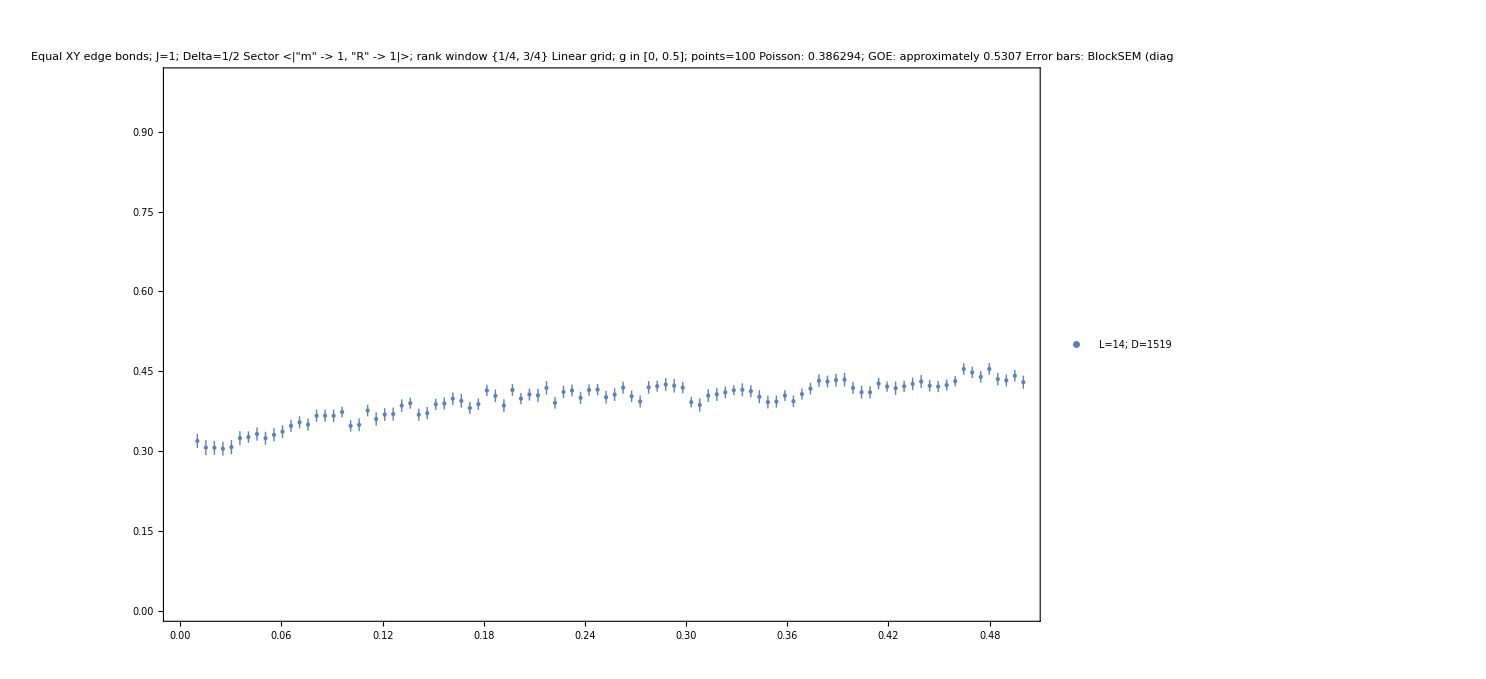

```mathematica
sgLinPlot=sgPlot[sgLinRun,sgLinStyle];
sgLinPlot
```

#### 13.3.4 Export this run

```mathematica
sgLinDirectory=sgExport[sgLinRun,sgLinPlot,sgLinStyle,
 sgLinOutputRoot,sgLinRunLabel];
```

Saved: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_selected_sector_results\Linear_g

Style-only changes require only the plot/export cells. Changing L, sector, J, Delta, g grid, precision, rank window or numerical tolerances requires regenerating the grid and recomputing this run. Exports contain settings actually used, actual labels and dimensions, all g values, raw ratios, optional full selected-sector spectra, diagnostics and the plot. New numbered folders preserve earlier runs. A supplied g=0 is retained as a diagnostic endpoint with no mean.

### 13.4. Independent log g grid: editable parameters

```mathematica
sgLogConfig=<|
 "Sector"->Automatic,  (* Or <|"m"->0,"R"->1,"F"->1|>, or <|"m"->1,"R"->-1|>. *)
 "LValues"->{14},"J"->1,"Delta"->1/2,
 "Grid"->"Log","gMin"->10^(-4),"gMax"->10^(-1),"gPoints"->100,
 "MinimumDimension"->400,"RankWindow"->{1/4,3/4},
 "GapResolution"->10^-10,"ValidationTolerance"->10^-10,
 "WorkingPrecision"->MachinePrecision,"BlockLength"->10,"StoreEnergies"->True|>;
sgLogStyle=<|"MarkerSize"->3,"ErrorBar"->"BlockSEM","ImageSize"->1100,"UseMaTeX"->True|>;
sgLogOutputRoot=FileNameJoin[{sgBaseFolder[],"xxz_selected_sector_results"}];
sgLogRunLabel="Log_g";
```

#### 13.4.1 Generate the grid and inspect exact sector sizes

```mathematica
sgLogUsed=sgValidate[sgLogConfig];
sgLogGrid=sgGrid[sgLogUsed];
sgLogDimensions=Table[With[{lab=sgLabels[l,sgLogUsed["Sector"]]},
 <|"L"->l,"Labels"->lab,"Dimension"->sgDimension[l,lab]|>],{l,sgLogUsed["LValues"]}];
Dataset[sgLogDimensions]
```

#### 13.4.2 Construct the selected block and compute its full spectrum at every g

```mathematica
sgCheck[sgLogConfig===sgLogUsed,"Parameters changed: regenerate the grid first."];
sgLogRun=sgScan[sgLogUsed,sgLogGrid];
Dataset[KeyDrop[#,{"Ratios","Energies"}]& /@ sgLogRun["Results"]]
```

Building L=14; sector <|m→1,R→1|>; D=1519

#### 13.4.3 Plot the retained means and diagnostic error bars

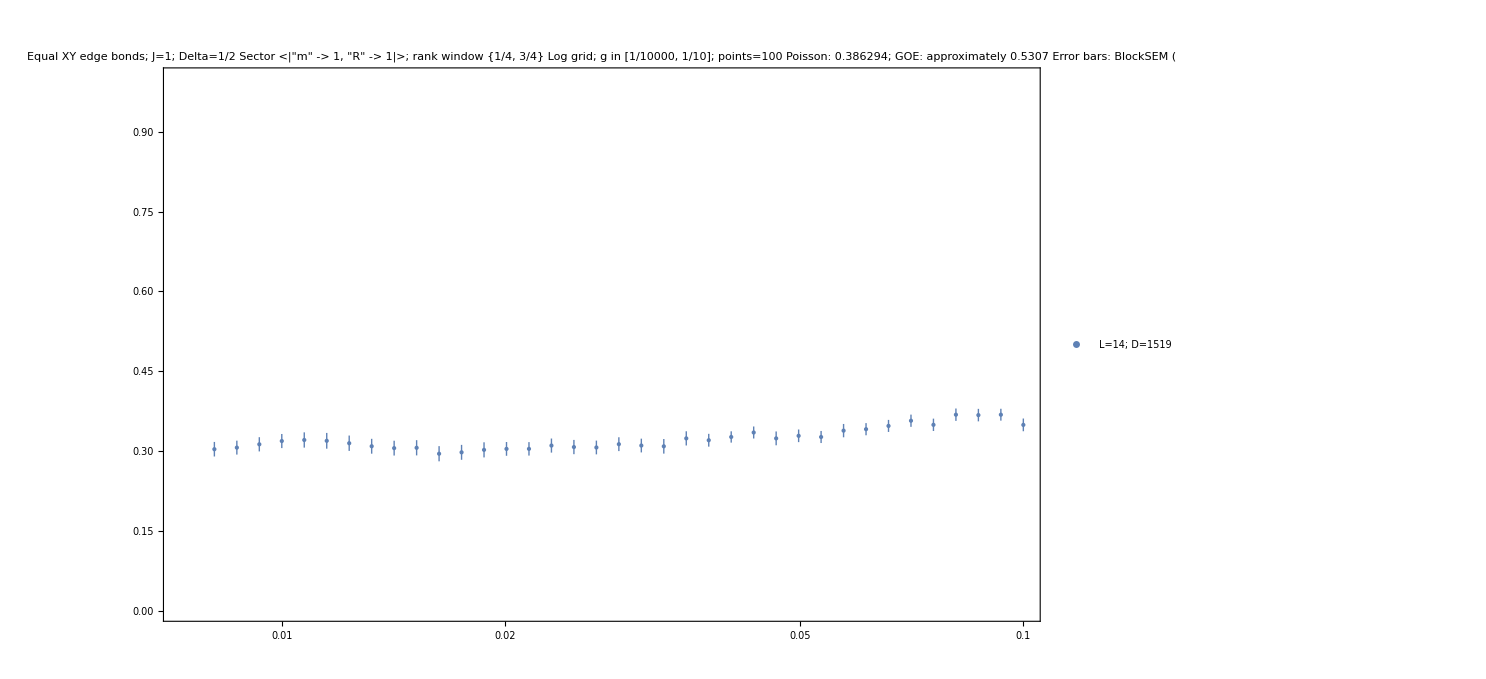

```mathematica
sgLogPlot=sgPlot[sgLogRun,sgLogStyle];
sgLogPlot
```

#### 13.4.4 Export this run

```mathematica
sgLogDirectory=sgExport[sgLogRun,sgLogPlot,sgLogStyle,
 sgLogOutputRoot,sgLogRunLabel];
```

Saved: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_selected_sector_results\Log_g_2

Style-only changes require only the plot/export cells. Changing L, sector, J, Delta, g grid, precision, rank window or numerical tolerances requires regenerating the grid and recomputing this run. Exports contain settings actually used, actual labels and dimensions, all g values, raw ratios, optional full selected-sector spectra, diagnostics and the plot. New numbered folders preserve earlier runs. The log grid contains no zero or negative g. Only the horizontal g/|J| axis is logarithmic; the ratio axis remains linear.